## init

```mathematica
d=5;FS=FullSimplify;
ηM=DiagonalMatrix[{-1,1,1,1,1}]; Subscript[η, i_,j_]:=ηM[[i+1,j+1]];
(*Δ[r]:=r^2-2M r+a^2; ρ[r,θ]:=√(r^2+a^2 Cos[θ]^2);*)(* Clear[ρ,Δ,M,a];*)
(*At=dt-a Sin[θ]^2 dϕ;Aϕ=dϕ-a/ρ[r,θ]^2 At;*)
(*ds2=E^(2nu[t,z])B[t,z]^((-(d-3))/(d-2))(-dt^2+dz^2)+B[t,z]^(2/(d-2))(dχ^2/(1-ku χ^2)+χ^2(Sin[θ]^2 dϕ^2+dθ^2));*)
ds2=-V[r] dt^2+dr^2/V[r]+r^2(dθ^2+Sin[θ]^2(dϕ^2+Sin[ϕ]^2 dψ^2))(*(dχ^2/(1-ku χ^2)+χ^2(Sin[θ]^2 dϕ^2+dθ^2))*);

dX={dt,dr,dθ,dϕ,dψ}(*{dt,dr,dχ,dϕ,dθ}*); Subscript[x, i_]:={t,r,θ,ϕ,ψ}(*{t,r,χ,ϕ,θ}*)[[i+1]];
gM=Table[1/2 D[D[ds2, dX[[j]]], dX[[i]]],{i,1,d},{j,1,d}];
(*f[r]=(r-rp)(r-rm)/r^2;*)
Subscript[g, i_,j_]:=gM[[i+1,j+1]];
giM=Inverse[gM];Subscript[gi, i_,j_]:=giM[[i+1,j+1]];

Text[Connection Subscript[Γ, μ]^ab];
Subscript[Γ, μ_,a_,b_]:=1/2 Sum[Subscript[gi, μ,ν](D[Subscript[g, b,ν], Subscript[x, a]]+D[Subscript[g, ν,a], Subscript[x, b]]-D[Subscript[g, b,a], Subscript[x, ν]]),{ν,0,d-1}];

Text[Curvature Subscript[R, μν]^ab];
Subscript[R, μ_,s_,m_,n_]:=(D[Subscript[Γ, μ,n,s], Subscript[x, m]]-D[Subscript[Γ, μ,m,s], Subscript[x, n]])+Sum[Subscript[Γ, μ,m,c] Subscript[Γ, c,n,s]-Subscript[Γ, μ,n,c] Subscript[Γ, c,m,s],{c,0,d-1}];
Text[Ricci Tensor Subscript[R, ab]];
Subscript[R, a_,b_]:=Sum[Subscript[R, k,a,k,b],{k,0,d-1}];
Text[Ricci Scalar Ri];
(*Ri=Sum[Subscript[gi, a,b] Subscript[R, a,b],{a,0,d-1},{b,0,d-1}];*)
Text["Covariant Derivative ∇g. First index is for g, second for ∇"];
∇Subscript[g_, μ_,i_]:=D[Subscript[g, μ], Subscript[x, i]]+Sum[Subscript[Γ, μ,i,j] Subscript[g, j],{j,0,d-1}]; (*Contravariant*)
∇Subscript[g_, 1,j_,i_]:=D[Subscript[g, j], Subscript[x, i]]-Sum[Subscript[Γ, μ,i,j] Subscript[g, μ],{μ,0,d-1}];(*Covariant*)
Text[Surface Gravity κ];
κ[ζ_]:={Subscript[ζl, μ_]:=∑_(i=0)^(d-1) Subscript[g, μ,i] Subscript[ζ, i];
Sqrt[-Sum[∑_(μ=1)^(d-1) (∇Subscript[ζ, i,j] Subscript[gi, j,μ]∇Subscript[ζl, 1,i,μ]),{i,0,d-1},{j,0,d-1}]]}[[1]];
```

```mathematica
Clear[V];
Subscript[Γ, i_]:=Table[FS[Subscript[Γ, j,k,i]],{j,0,d-1},{k,0,d-1}];
Subscript[GB1, i_]:=FS[Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,0]/.->1]
Ri=FS[Sum[Subscript[gi, a,b] Subscript[R, a,b],{a,0,d-1},{b,0,d-1}]/.->1];
```

```mathematica
GBt1=FS[Subscript[R, 1,1] Subscript[gi, 1,1] Subscript[gi, 1,1] Subscript[Γ, 0,1,0]/.->1];
(*GB1=FS[Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,0]+a/(a^2+r^2)Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,1]/.->1]*)
GBR2= FS[Table[(Subscript[R, j,k,1,0] Subscript[gi, 0,0])Subscript[gi, 1,1]/.->1,{j,0,d-1},{k,0,d-1}]];
GBt2=FS[Sum[GBR2[[j+1,k+1]] Subscript[g, j,l] Subscript[gi, k,m](Subscript[Γ, 0][[l+1,m+1]]),{j,0,d-1},{k,0,d-1},{l,0,d-1},{m,0,d-1}]]
(*GB2=FS[Sum[GBR2[[j+1,k+1]] Subscript[g, j,l] Subscript[gi, k,m](Subscript[Γ, 0][[l+1,m+1]]+a/(a^2+r^2)Γϕ[[l+1,m+1]]),{j,0,3},{k,0,3},{l,0,3},{m,0,3}]]*)
GBt=FS[(Ri Subscript[Γ, 1,0,0] Subscript[gi, 0,0]+ 4 GBt1+GBt2)]
```

1/2 V'(r) V''(r)

(3 (V(r)-1) V'(r))/r^2

```mathematica
V[r_]:=κ+r^2/(2α)(1-Sqrt[1+4α(μ/r^(n-1)-q2/r^(2(n-2))+2Λ)]);
```

## Calculations

```mathematica
Clear[α,αs]
```

```mathematica
sb={αs-> -2(n-2)(n-3)κ α2, α->-(n-3)(n-4)α2}; sub={μ->(16π M)/((n-2)Σ),q2->(4π q^2)/(2π(n-2)(n-3)),Λ->Λ1/((n-1)(n-2))};
```

```mathematica
Subscript[G, j_]:={(-(-αs)^(n-3)(μ/κ)^2+(κ α (-αs)^(n-4)+(-αs)^(n-3)+q2/κ)^2)/.sb,(-(-αs)^((n-3)/2)μ/κ+κ α (-αs)^(n-4)+(-αs)^(n-3)+q2/κ)^2}[[j]]
```

```mathematica
/.αs->2 α/κ (n-2)/(n-4)
```

```mathematica
αs->2 α/κ (n-2)/(n-4)/.α->-(n-3)(n-4)α2
```

2 α2 (3-n) (n-2)

```mathematica
Subscript[G, 1]/.sub/.{n->4,κ->1}/.Σ-> 4π
```

(4 α2+q^2)^2-16 α2 M^2

```mathematica
FS[r^2+q2/r^2/.solm[[2,1]]]
```

μ-α

```mathematica
FS[Subscript[G, 2]/.{n->5,κ->1}]
```

(αs (-α+αs+μ)+q2)^2

```mathematica
Clear[V]
```

```mathematica
Eee=FS[-2 r^3((-V'[r])/(16π)+ α1 GBt/.α1->α/(32 π))];
See=FS[2π Eee/V'[r]/.V[r]->0];
```

```mathematica
See
```

1/8 r (3 α c+2 r^2)

```mathematica
V[r_]:=κ+r^2/(2α)(1-Sqrt[1+4α(μ/r^(n-1)-q2/r^(2(n-2))+2Λ)])/.{κ->1,n->5,Λ->0};
solm=FS[Solve[V[r]==0,r]]
```

{{r→-(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→-(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)}}

```mathematica
Expand[(r-r1)(r-r2)(r-r3)]
```

r^3-r^2 r1-r^2 r2-r^2 r3+r r1 r2+r r1 r3+r r2 r3-r1 r2 r3

```mathematica
FS[Product[See/.solm[[i,1]],{i,1,4}]]
```

1/256 q2 (6 α (5 α+μ)+q2)^2

```mathematica
V[r_]:=ku-r^2 f[r]/.ku->1;
```

```mathematica
f[r_]:=μ/r^(d-1)+h[r];
h[r_]:=-Q^2/r^(2(d-2));
```

```mathematica
FS[Table[Subscript[R, i,j]-1/2 Ri Subscript[g, i,j]/.->1,{i,0,d-1},{j,0,d-1}]/gM]
```

Power::infy: Infinite expression TraditionalForm`1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression TraditionalForm`0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

(-(3 Q^2)/r^6 | Indeterminate | Indeterminate | Indeterminate | Indeterminate
Indeterminate | -(3 Q^2)/r^6 | Indeterminate | Indeterminate | Indeterminate
Indeterminate | Indeterminate | (3 Q^2)/r^6 | Indeterminate | Indeterminate
Indeterminate | Indeterminate | Indeterminate | (3 Q^2)/r^6 | Indeterminate
Indeterminate | Indeterminate | Indeterminate | Indeterminate | (3 Q^2)/r^6)

```mathematica
Eee=FS[-2 r^3((-V'[r])/(16π)+4α1 GBt/.α1->α/(32 π))]
```

(r (6 α+r^2-6 α V(r)) V'(r))/(8 π)

```mathematica
See=FS[2π Eee/V'[r]/.V[r]->0]
```

1/4 r (6 α+r^2)

```mathematica
solm=FS[Solve[V[r]==0,r]]
```

{{r→-(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→-(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)}}

```mathematica
{{r->1/2 (μ-√(μ^2-4 (α+q2)))},{r->1/2 (μ+√(μ^2-4 (α+q2)))}}
```

```mathematica
FS[Product[(See/.solm[[i,1]]),{i,1,4}]]
```

1/256 q2 (6 α (5 α+μ)+q2)^2

```mathematica
Limit[Eee,r->∞]
```

μ/(4 π)

```mathematica
Limit[V[r],α->0]
```

(q2+r^2-μ r)/r^2

```mathematica
Limit[r^5 V'[r]/2,r->∞]
```

2 μ

```mathematica
FS[GBt]
```

-(3 (√(-(4 α q2)/r^6+(4 α μ)/r^4+1)-1) (r^6 (√(-(4 α q2)/r^6+(4 α μ)/r^4+1)-1)-2 α q2))/(2 α^2 r^5 √(-(4 α q2)/r^6+(4 α μ)/r^4+1))

```mathematica
2 π^((n-1)/2)Gamma[(n-1)/2]/.n->5
```

2 π^2

```mathematica
V[r]/.
```

(r^2 (1-√(4 α (μ/r^4-q2/r^6)+1)))/(2 α)+1

```mathematica
solm=FS[Solve[V[r]==0,r]]
```

{{r→-(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→-(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)}}

```mathematica
solm[[3,1]]
```

r→-(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)

```mathematica
r/.solm[[3,1]]/.{q2->1,α->2,μ->4}
```

-1

```mathematica
FS[V[r]/.solm[[2,1]]/.q2->0]
```

((√((α-μ)^2)+α-μ) (√((16 α μ)/((√((α-μ)^2)+α-μ)^2)+1)-1))/(4 α)+1

1-((-α+μ+√((α-μ)^2-4 q2)) (√(1-(16 α (2 q2-μ (-α+μ+√((α-μ)^2-4 q2))))/((-α+μ+√((α-μ)^2-4 q2))^3))-1))/(4 α)

```mathematica
Subscript[Γ, 1,0,0]
```

1/2 V(r) V'(r)

```mathematica
Clear[V]
```

$Aborted

```mathematica
so=Solve[α==16π α1 (n-3)(n-4)/.n->5,α1]
```

{{α1→α/(32 π)}}

```mathematica
α1->α/(32 π)
```

```mathematica
α==16π α1 (n-3)(n-4)
```

α==16 π α1 (n-4) (n-3)

```mathematica
Clear[V]
```

```mathematica
Subscript[gi, 0,0] Subscript[Γ, 1,0,0]
```

-1/2 V'(r)

```mathematica
Eee=FS[-2 r^3((-V'[r])/(16π)+4α1 GBt/.so[[1,1]])]
```

(r (6 α+r^2-6 α V(r)) V'(r))/(8 π)

```mathematica
See=FS[4π Eee/V'[r]/.V[r]->0]
```

1/2 r (6 α+r^2)

```mathematica
FS[(See/.solm[[3,1]])(See/.solm[[1,1]])]
```

1/8 √(-α+μ-√((α-μ)^2-4 q2)) √(-α+μ+√((α-μ)^2-4 q2)) (6 α (5 α+μ)+q2)

```mathematica
Assuming[α-μ>0,FS[V[r]/.solm[[3,1]]/.q2->0]]
```

Indeterminate

```mathematica
V[r]/.solm[[1,1]]/.{q2->0,μ->1,α->3}
```

4/3

```mathematica
Limit[V[r]/.solm[[1,1]]/.q2->0,α->0]
```

(√(μ^2)+μ)/(√(μ^2)-μ)

```mathematica
Limit[Eee,r->∞]
```

μ/(4 π)

```mathematica
Assuming[(α-μ)^2-4 q2^2>0,FS[Eee/.solm[[2,1]]]]
```

1/(16 √2 π)(-α+μ-√((α-μ)^2-4 q2))^(3/2) (3 √((16 α (μ (α-μ+√((α-μ)^2-4 q2))+2 q2))/((α-μ+√((α-μ)^2-4 q2))^3)+1)-2) (-(8 √2 (μ (α-μ+√((α-μ)^2-4 q2))+3 q2))/((-α+μ-√((α-μ)^2-4 q2))^(5/2) √((16 α (μ (α-μ+√((α-μ)^2-4 q2))+2 q2))/((α-μ+√((α-μ)^2-4 q2))^3)+1))-(√(-α+μ-√((α-μ)^2-4 q2)) (√((16 α (μ (α-μ+√((α-μ)^2-4 q2))+2 q2))/((α-μ+√((α-μ)^2-4 q2))^3)+1)-1))/(√2 α))

```mathematica
Limit[%/.{q2->0},α->0]
```

μ^2/(2 π μ-2 π √(μ^2))

```mathematica
1/(16 √2 π)(-α+μ-√((α-μ)^2-4 q2))^(3/2) (3 √((16 α (μ (α-μ+√((α-μ)^2-4 q2))+2 q2))/((α-μ+√((α-μ)^2-4 q2))^3)+1)-2) (-(8 √2 (μ (α-μ+√((α-μ)^2-4 q2))+3 q2))/((-α+μ-√((α-μ)^2-4 q2))^(5/2) √((16 α (μ (α-μ+√((α-μ)^2-4 q2))+2 q2))/((α-μ+√((α-μ)^2-4 q2))^3)+1))-(√(-α+μ-√((α-μ)^2-4 q2)) (√((16 α (μ (α-μ+√((α-μ)^2-4 q2))+2 q2))/((α-μ+√((α-μ)^2-4 q2))^3)+1)-1))/(√2 α))
```

```mathematica
Limit[%,r->∞]
```

0

```mathematica
Assuming[n∈Integers&&n>1, Limit[r^(n-2)V'[r],r->∞]]
```

lim_(r→∞) r^(n-2) ((r (1-√(4 α (2 Λ-q2 r^(-2 (n-2))+μ r^(1-n))+1)))/α-(r^2 (2 (n-2) q2 r^(-2 (n-2)-1)+μ (1-n) r^-n))/(√(4 α (2 Λ-q2 r^(-2 (n-2))+μ r^(1-n))+1)))

```mathematica
Integrate[Sin[θ]^2 Sin[ϕ] r^3,{θ,0,π},{ϕ,0,π}]
```

π r^3

```mathematica
Limit[%,α->0]
```

-(2 sin^2(θ) sin(ϕ) (2 q2-μ r^2) (2 q2^2+q2 (r^4-5 μ r^2)+3 μ r^4 (μ-r^2)))/(r^8 (q2+r^4-μ r^2))

```mathematica
%/.q2->0
```

(6 μ^2 sin^2(θ) (μ-r^2) sin(ϕ))/(r^2 (r^4-μ r^2))

```mathematica
Clear[V]
```

```mathematica
FS[Ri]
```

-(6 (r V'(r)+V(r)-1))/r^2-V''(r)

```mathematica
V[r_]:=1-r^2 f[r]
```

```mathematica
FS[Ri]
```

r (r f''(r)+10 f'(r))+20 f(r)

```mathematica
FS[Table[Subscript[R, i,j]/.->1,{i,0,d-1},{j,0,d-1}]]
```

((V(r) (3 V'(r)+r V''(r)))/(2 r) | 0 | 0 | 0 | 0
0 | -(3 V'(r)+r V''(r))/(2 r V(r)) | 0 | 0 | 0
0 | 0 | -2 V(r)-r V'(r)+2 | 0 | 0
0 | 0 | 0 | -sin^2(θ) (2 V(r)+r V'(r)-2) | 0
0 | 0 | 0 | 0 | -sin^2(θ) sin^2(ϕ) (2 V(r)+r V'(r)-2))

```mathematica
FS[Table[Subscript[R, 0,1,i,j]/.->1,{i,0,d-1},{j,0,d-1}]]
```

(0 | -(V''(r))/(2 V(r)) | 0 | 0 | 0
(V''(r))/(2 V(r)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[Γ, 0,0,1]
```

(V'(r))/(2 V(r))

```mathematica
Subscript[Γ, 0]
```

(0 | (V'(r))/(2 V(r)) | 0 | 0 | 0
1/2 V(r) V'(r) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
FS[Ri]
```

(16 α^2 q2^2-72 α^2 μ q2 r^2+α q2 r^6 (40 √(-(4 α q2)/r^6+(4 α μ)/r^4+1)-62)-10 r^12 (√(-(4 α q2)/r^6+(4 α μ)/r^4+1)-1)+α μ r^8 (60-40 √(-(4 α q2)/r^6+(4 α μ)/r^4+1))+48 α^2 μ^2 r^4)/(α r^6 √(-(4 α q2)/r^6+(4 α μ)/r^4+1) (-4 α q2+r^6+4 α μ r^2))

```mathematica
Assuming[r>0,FS[Ri-(16 α^2 q2^2-72 α^2 μ q2 r^2+48 α^2 μ^2 r^4-62α q2 r^6 +10 r^12 +α μ r^8 (60 ))/(α r^3(-4 α q2+r^6+4 α μ r^2)^(3/2))+10/α]]
```

0

```mathematica
Ri0=FS[Ri]
```

(48 α^2 μ^2+20 α μ r^4 (3-2 √((4 α μ)/r^4+1))-10 r^8 (√((4 α μ)/r^4+1)-1))/(α r^4 (4 α μ+r^4) √((4 α μ)/r^4+1))

```mathematica
FS[Ri0-2(5(((r^4+4α μ) -α μ)^2-4 α^2 μ^2)-α^2 μ^2)/(α r^2 (4 α μ+r^4)^(3/2))+10/α]
```

(2 (24 α^2 μ^2+5 r^8+30 α μ r^4) (-4 α μ-r^4+r^2 √(4 α μ+r^4) √((4 α μ)/r^4+1)))/(α r^2 (4 α μ+r^4)^(5/2))

```mathematica
Assuming[r>0,FS[Ri-2(5(((-4α q2+4 α μ r^2+r^6) -α μ r^2+α q2)^2-4(-α μ r^2+α q2)^2)-(-α μ r^2+α q2)^2)/(α r^3(-4α q2+4 α μ r^2+r^6)^(3/2))+10/α]]
```

-(2 q2 (16 α q2+r^6-12 α μ r^2))/(r^3 (-4 α q2+r^6+4 α μ r^2)^(3/2))

```mathematica
Clear[g]
```

```mathematica
w=r Cos[θ];
z=r Sin[θ]Cos[ϕ];
x=r Sin[θ]Sin[ϕ]Cos[ψ];
y=r Sin[θ]Sin[ϕ]Sin[ψ];
```

```mathematica
ds=D[{x,y,z,w},{{r,θ,ϕ,ψ}}].{dr,dθ,dϕ,dψ};
```

```mathematica
FS[Series[ds.ds,{r,0,2}]]
```

dr^2+1/4 r^2 (4 dθ^2-2 dψ^2 sin^2(θ) cos(2 ϕ)+dψ^2-(dψ^2+2 dϕ^2) cos(2 θ)+2 dϕ^2)+O(r^3)

```mathematica
FS[ds.ds-dr^2-r^2(dθ^2+Sin[θ]^2(dϕ^2+Sin[ϕ]^2 dψ^2))]
```

0

### Horizons in 5D, Λ=0

```mathematica
Clear[V]
```

```mathematica
V[r_]:=κ+r^2/(2α)(1-Sqrt[1+4α(μ/r^(n-1)-q2/r^(2(n-2))+2Λ)])
```

```mathematica
FS[V'[r]]
```

(r (-8 α Λ+√(8 α Λ-4 α q2 r^(4-2 n)+4 α μ r^(1-n)+1)-1)-2 α (n-4) q2 r^(5-2 n)+α μ (n-5) r^(2-n))/(α √(8 α Λ-4 α q2 r^(4-2 n)+4 α μ r^(1-n)+1))

```mathematica
solm=FS[Solve[V[r]==0/.{n->5,Λ->0},r]]
```

{{r→-(√((-α κ^2+μ+√((μ-α κ^2)^2-4 κ q2))/κ))/(√2)},{r→(√((-α κ^2+μ+√((μ-α κ^2)^2-4 κ q2))/κ))/(√2)},{r→-(√((-α κ^2+μ-√((μ-α κ^2)^2-4 κ q2))/κ))/(√2)},{r→(√((-α κ^2+μ-√((μ-α κ^2)^2-4 κ q2))/κ))/(√2)}}

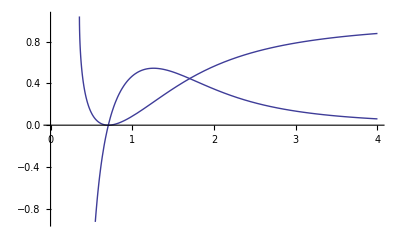

```mathematica
Plot[{V[r],V'[r]}/.{n->5,Λ->0,α->1,q2->.25,μ->2,κ->1},{r,0,4}]
```

```mathematica
solmd=Solve[V'[r]==0/.{n->5,Λ->0},r]
```

{{r→-√(q2/(2 μ)-1/2 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ))-1/2 √(-(2 q2^3)/(μ^3 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))+(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+(2 q2^2)/μ^2-(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))},{r→√(q2/(2 μ)-1/2 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ))-1/2 √(-(2 q2^3)/(μ^3 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))+(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+(2 q2^2)/μ^2-(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))},{r→-√(q2/(2 μ)-1/2 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ))+1/2 √(-(2 q2^3)/(μ^3 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))+(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+(2 q2^2)/μ^2-(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))},{r→√(q2/(2 μ)-1/2 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ))+1/2 √(-(2 q2^3)/(μ^3 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))+(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+(2 q2^2)/μ^2-(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))},{r→-√(q2/(2 μ)+1/2 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ))-1/2 √((2 q2^3)/(μ^3 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))+(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+(2 q2^2)/μ^2-(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))},{r→√(q2/(2 μ)+1/2 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ))-1/2 √((2 q2^3)/(μ^3 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))+(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+(2 q2^2)/μ^2-(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))},{r→-√(q2/(2 μ)+1/2 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ))+1/2 √((2 q2^3)/(μ^3 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))+(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+(2 q2^2)/μ^2-(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))},{r→√(q2/(2 μ)+1/2 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ))+1/2 √((2 q2^3)/(μ^3 √(-(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+q2^2/μ^2+(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))+(2 2^(2/3) α q2^2)/(3^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))+(2 q2^2)/μ^2-(2^(1/3) (√3 √(27 α^2 q2^8+16 α^3 μ^3 q2^6)-9 q2^4 α)^(1/3))/(3^(2/3) μ)))}}

```mathematica
solm[[1,1]]
```

r→-(√((-α κ^2+μ+√((μ-α κ^2)^2-4 κ q2))/κ))/(√2)

```mathematica
FS[V'[r]/.{n->5,Λ->0}]
```

(r^6 (√(-(4 α q2)/r^6+(4 α μ)/r^4+1)-1)-2 α q2)/(α r^5 √(-(4 α q2)/r^6+(4 α μ)/r^4+1))

```mathematica
FS[V'[r]/.{n->5,Λ->0}/.q2->(μ-α κ^2)^2/(4 κ )]
```

(-α (μ-α κ^2)^2-2 κ r^6+2 κ r^6 √(-(α (μ-α κ^2)^2)/(κ r^6)+(4 α μ)/r^4+1))/(2 α κ r^5 √(-(α (μ-α κ^2)^2)/(κ r^6)+(4 α μ)/r^4+1))

```mathematica
FS[%/.r->√((-α κ^2+μ)/(2κ))]
```

(√(μ/κ-α κ) (α κ^2 (√(((3 α κ^2+μ)^2)/((μ-α κ^2)^2))+3)-μ √(((3 α κ^2+μ)^2)/((μ-α κ^2)^2))+μ))/(√2 α (3 α κ^2+μ))

```mathematica
(-√(μ-α κ^2)+(3α κ^2 √(μ-α κ^2))/(3 α κ^2+μ)+(μ √(μ-α κ^2))/(3 α κ^2+μ))/(√(2κ) α)
```

((3 α κ^2 √(μ-α κ^2))/(3 α κ^2+μ)-√(μ-α κ^2)+(μ √(μ-α κ^2))/(3 α κ^2+μ))/(√2 α √κ)

```mathematica
FS[%]
```

0

```mathematica
FS[%/.{α->1,μ->2,κ->1}]
```

0

```mathematica
FS[%/.solm[[1,1]]]
```

-(4 (((-α κ^2+μ+√((μ-α κ^2)^2-4 κ q2))^3 (√(1-(16 α κ^2 (2 κ q2-μ (-α κ^2+μ+√((μ-α κ^2)^2-4 κ q2))))/((-α κ^2+μ+√((μ-α κ^2)^2-4 κ q2))^3))-1))/(8 κ^3)-2 α q2))/(α ((-α κ^2+μ+√((μ-α κ^2)^2-4 κ q2))/κ)^(5/2) √((8 α κ^2 (μ (-α κ^2+μ+√((μ-α κ^2)^2-4 κ q2))-2 κ q2))/((-α κ^2+μ+√((μ-α κ^2)^2-4 κ q2))^3)+1/2))

```mathematica
Assuming[(μ-α κ^2)^2-4 κ q2==0,FS[%]]
```

-(κ^2 √(μ/κ-α κ) (3 κ q2 (2 √((4 α κ^2 μ^2-4 μ^3+9 α κ^3 q2+15 κ μ q2)/((α κ^2-μ)^3))+3)+2 μ (α κ^2 (√((4 α κ^2 μ^2-4 μ^3+9 α κ^3 q2+15 κ μ q2)/((α κ^2-μ)^3))+3)-μ (√((4 α κ^2 μ^2-4 μ^3+9 α κ^3 q2+15 κ μ q2)/((α κ^2-μ)^3))+1))))/(√2 (10 α κ^2 μ^2-6 μ^3+9 α κ^3 q2+24 κ μ q2))

```mathematica
FS[%/.q2-> (μ-α κ^2)^2/(4 κ)]
```

-(√(μ/κ-α κ) (α κ^2 (√(((3 α κ^2+μ)^2)/((μ-α κ^2)^2))+3)-μ √(((3 α κ^2+μ)^2)/((μ-α κ^2)^2))+μ))/(√2 α (3 α κ^2+μ))

```mathematica
solm=FS[Solve[V[r]==0/.n->5,r]]
```

```mathematica
sol=%;
```

{{r→-1/(√6)(√((κ^2+(κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(1/3) κ-6 Λ μ+(κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(2/3))/(Λ (κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(1/3))))},{r→1/(√6)(√((κ^2+(κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(1/3) κ-6 Λ μ+(κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(2/3))/(Λ (κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(1/3))))},{r→-1/(2 √3)(√(((6-6 ⅈ √3) Λ μ+((κ^3-9 Λ μ κ+54 q2 Λ^2+3 √3 √(Λ^2 (8 Λ μ^3-κ^2 μ^2-36 q2 κ Λ μ+4 q2 (κ^3+27 q2 Λ^2))))^(1/3)-κ) (-ⅈ √3 κ+κ+(-1-ⅈ √3) (κ^3-9 Λ μ κ+54 q2 Λ^2+3 √3 √(Λ^2 (8 Λ μ^3-κ^2 μ^2-36 q2 κ Λ μ+4 q2 (κ^3+27 q2 Λ^2))))^(1/3)))/(Λ (κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(1/3))))},{r→1/(2 √3)(√(((6-6 ⅈ √3) Λ μ+((κ^3-9 Λ μ κ+54 q2 Λ^2+3 √3 √(Λ^2 (8 Λ μ^3-κ^2 μ^2-36 q2 κ Λ μ+4 q2 (κ^3+27 q2 Λ^2))))^(1/3)-κ) (-ⅈ √3 κ+κ+(-1-ⅈ √3) (κ^3-9 Λ μ κ+54 q2 Λ^2+3 √3 √(Λ^2 (8 Λ μ^3-κ^2 μ^2-36 q2 κ Λ μ+4 q2 (κ^3+27 q2 Λ^2))))^(1/3)))/(Λ (κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(1/3))))},{r→-1/(2 √3)(√(((6+6 ⅈ √3) Λ μ+((κ^3-9 Λ μ κ+54 q2 Λ^2+3 √3 √(Λ^2 (8 Λ μ^3-κ^2 μ^2-36 q2 κ Λ μ+4 q2 (κ^3+27 q2 Λ^2))))^(1/3)-κ) (ⅈ √3 κ+κ+ⅈ (ⅈ+√3) (κ^3-9 Λ μ κ+54 q2 Λ^2+3 √3 √(Λ^2 (8 Λ μ^3-κ^2 μ^2-36 q2 κ Λ μ+4 q2 (κ^3+27 q2 Λ^2))))^(1/3)))/(Λ (κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(1/3))))},{r→1/(2 √3)(√(((6+6 ⅈ √3) Λ μ+((κ^3-9 Λ μ κ+54 q2 Λ^2+3 √3 √(Λ^2 (8 Λ μ^3-κ^2 μ^2-36 q2 κ Λ μ+4 q2 (κ^3+27 q2 Λ^2))))^(1/3)-κ) (ⅈ √3 κ+κ+ⅈ (ⅈ+√3) (κ^3-9 Λ μ κ+54 q2 Λ^2+3 √3 √(Λ^2 (8 Λ μ^3-κ^2 μ^2-36 q2 κ Λ μ+4 q2 (κ^3+27 q2 Λ^2))))^(1/3)))/(Λ (κ^3-9 Λ μ κ+54 q2 Λ^2+1/2 √(4 (κ^3-9 Λ μ κ+54 q2 Λ^2)^2-4 (κ^2-6 Λ μ)^3))^(1/3))))}}

```mathematica
Solve[μ/2==r^(n-3)+α r^(n-5)/.n->6,r]
```

{{r→(2^(2/3) α)/(3^(1/3) (√3 √(16 α^3+27 μ^2)-9 μ)^(1/3))-((√3 √(16 α^3+27 μ^2)-9 μ)^(1/3))/6^(2/3)},{r→((1-ⅈ √3) (√3 √(16 α^3+27 μ^2)-9 μ)^(1/3))/(2 6^(2/3))-((1+ⅈ √3) α)/(6^(1/3) (√3 √(16 α^3+27 μ^2)-9 μ)^(1/3))},{r→((1+ⅈ √3) (√3 √(16 α^3+27 μ^2)-9 μ)^(1/3))/(2 6^(2/3))-((1-ⅈ √3) α)/(6^(1/3) (√3 √(16 α^3+27 μ^2)-9 μ)^(1/3))}}

```mathematica
FS[V'[r]]
```

(r (-8 α Λ+√(8 α Λ-4 α q2 r^(4-2 n)+4 α μ r^(1-n)+1)-1)-2 α (n-4) q2 r^(5-2 n)+α μ (n-5) r^(2-n))/(α √(8 α Λ-4 α q2 r^(4-2 n)+4 α μ r^(1-n)+1))

```mathematica
Replace
```

```mathematica
Solve[V[r]==0,{μ,q}]
```

{{μ→q^2 r^(3-n)+ku r^(-3+n)+ku^2 r^(-5+n) α-2 r^(-1+n) Λ}}

```mathematica
Solve[V[r]==0,q2]
```

{{q2→r^(-8+n) (-r^(2+n) κ-r^n α κ^2+2 r^(4+n) Λ+r^5 μ)}}

```mathematica
Assuming[V[r]==0,FS[V'[r]/.Solve[V[r]==0,μ][[1]]]]
```

1/(α √(((r^2+2 ku α)^2)/r^4))r^(-3-2 n) (-(-3+n) q^2 r^8 α+ku (-5+n) r^(2+2 n) α+ku^2 (-5+n) r^(2 n) α^2+r^(4+2 n) (-1+√(((r^2+2 ku α)^2)/r^4)-2 (-1+n) α Λ))

```mathematica
FS[V'[r]]
```

(r (-8 α Λ+√(8 α Λ-4 α q2 r^(4-2 n)+4 α μ r^(1-n)+1)-1)-2 α (n-4) q2 r^(5-2 n)+α μ (n-5) r^(2-n))/(α √(8 α Λ-4 α q2 r^(4-2 n)+4 α μ r^(1-n)+1))

```mathematica
FS[(-2 (-4+n) q2 r^(5-2 n) α+(-5+n) r^(2-n) α μ+r (-1-8 α Λ+(-ϵ(r^2+2 κ α))/r^2))/(α (-ϵ(r^2+2 κ α))/r^2)]
```

(2 α (n-4) q2 r^(7-2 n)-α μ (n-5) r^(4-n)+r^3 (8 α Λ+ϵ+1)+2 α κ r ϵ)/(α ϵ (2 α κ+r^2))

```mathematica
FS[(2 α (n-4) q2 r^(7-2 n)-α μ (n-5) r^(4-n)+r^3 (8 α Λ+ϵ+1)+2 α κ r ϵ)/(α ϵ (2 α κ+r^2))/.Solve[V[r]==0,q2][[1]]]
```

(r^(-n-1) (α μ (n-3) r^5+r^n (-2 α^2 κ^2 (n-4)+r^4 (4 α Λ (n-2)+ϵ+1)+2 α κ r^2 (-n+ϵ+4))))/(α ϵ (2 α κ+r^2))

```mathematica
FS[(-2 (-4+n) q2 r^(7-2 n)+2 r κ-8 r^3 Λ+(-5+n) r^(4-n) μ)/(r^2+2 α κ)/.Solve[V[r]==0,q2][[1]]]
```

(r^(-n-1) (2 κ (n-3) r^(n+2)-4 Λ (n-2) r^(n+4)+2 α κ^2 (n-4) r^n-μ (n-3) r^5))/(2 α κ+r^2)

```mathematica
FS[%/.{Λ->0,μ->2κ r^(n-3)+(n-4)/(n-3)α κ^2 r^(n-5)}]
```

(-α^2 κ^2 (n-4)+r^4 (ϵ+1)+2 α κ r^2 (ϵ+1))/(α r ϵ (2 α κ+r^2))

```mathematica
FS[V'[r]/.Solve[V[r]==0,q2][[1]]/.{Λ->0,μ->2κ r^(n-3)+(n-4)/(n-3)α κ^2 r^(n-5)}]
```

(α^2 κ^2 (n-4)-2 α κ r^2+r^4 (√(((2 α κ+r^2)^2)/r^4)-1))/(α r^3 √(((2 α κ+r^2)^2)/r^4))

```mathematica
FS[(α^2 κ^2 (n-4)-2 α κ r^2+r^4 ((2 α κ+r^2)/r^2-1))/(α r^3 (2 α κ+r^2)/r^2)]
```

(α κ^2 (n-4))/(r^3+2 α κ r)

```mathematica
FS[(2 (-3+n) r^2 κ+2 (-4+n) α κ^2-4 (-2+n) r^4 Λ-(-3+n) r^(5-n) μ)/(r^2+2 α κ)+2κ]
```

(r^-n (-2 (-2+n) r^n (-κ (r^2+α κ)+2 r^4 Λ)-(-3+n) r^5 μ))/(r^2+2 α κ)

```mathematica
FS[%/.{Λ->0,κ->1,α->0,n->4}]
```

4-μ/r

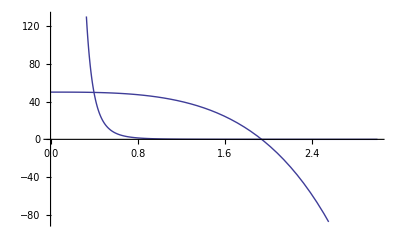

```mathematica
Plot[{50+0 r^(n-1)-.5 r^(n-3)-5 r^(n-5),0.5 r^(3-n)}/.n->8,{r,0,3}]
```

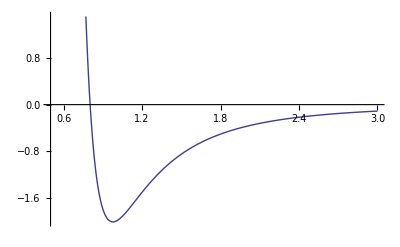

```mathematica
Plot[(r^(3-n)-3)r^(5-n)/.n->8,{r,.5,3}]
```

```mathematica
FS[%/.{Λ->0,κ->1,α->0,n->4}]
```

(2 r-μ)/r^2

```mathematica
FS[1/(α (r^2+2 ku α)/r^2)r^(-3-2 n) (-(-3+n) q^2 r^8 α+ku (-5+n) r^(2+2 n) α+ku^2 (-5+n) r^(2 n) α^2+r^(4+2 n) (-1+(r^2+2 ku α)/r^2-2 (-1+n) α Λ))]
```

1/(r^2+2 ku α)r^(-1-2 n) (-(-3+n) q^2 r^8+r^(2 n) (ku (-3+n) r^2+ku^2 (-5+n) α-2 (-1+n) r^4 Λ))

```mathematica
FS[(-2 (-4+n) q^2 r^(5-2 n) α+(-5+n) r^(2-n) α μ+r(r^2+2α ku)/r^2)/((r^2+2α ku)/r^2)]
```

(r^3+2 ku r α-2 (-4+n) q^2 r^(7-2 n) α+(-5+n) r^(4-n) α μ)/(r^2+2 ku α)

```mathematica
FS[%/.Solve[V[r]==0,μ][[1]]]
```

(r^(-1-2 n) (-(-3+n) q^2 r^8 α+r^(2 n) (ku (-3+n) r^2 α+ku^2 (-5+n) α^2+r^4 (1-2 (-5+n) α Λ))))/(r^2+2 ku α)

```mathematica
Expand[r^(-1-2 n) (-(-3+n) q^2 r^8 α+r^(2 n) (ku (-3+n) r^2 α+ku^2 (-5+n) α^2+r^4 (1-2 (-5+n) α Λ))),r]
```

ku (-3+n) r α+(3-n) q^2 r^(7-2 n) α+(ku^2 (-5+n) α^2)/r+r^3 (1-2 (-5+n) α Λ)

```mathematica
Integrate[(r^2+a^2 Cos[θ]^2)Sin[θ]/r^2,{θ,0,π}]
```

(2 a^2)/(3 r^2)+2

```mathematica
dS=FS[D[r^2+a^2/.r->M+Sqrt[M^2-a^2-q^2],{{M,a,q}}](Sqrt[M^2-a^2-q^2]/(r^2+a^2)/.r->M+Sqrt[M^2-a^2-q^2])].{dM,da,dq}
```

-(2 a da M)/(2 M (√(-a^2+M^2-q^2)+M)-q^2)+(2 dM (√(-a^2+M^2-q^2)+M)^2)/(2 M (√(-a^2+M^2-q^2)+M)-q^2)-(2 dq q (√(-a^2+M^2-q^2)+M))/((√(-a^2+M^2-q^2)+M)^2+a^2)

```mathematica
FS[FS[D[r^2+a^2/.r->M+Sqrt[M^2-a^2-q^2],{{M,a,q}}] (Sqrt[M^2-a^2-q^2]/(r^2+a^2)/.r->M+Sqrt[M^2-a^2-q^2])].{dM,da,dq}-2(dM-a(da M+dM a)/(r^2+a^2)-q dq r/(r^2+a^2) /.r->M+Sqrt[M^2-a^2-q^2])]
```

0

```mathematica
Ri=FS[Sum[Subscript[gi, a,b] Subscript[R, a,b]/.->1,{a,0,d-1},{b,0,d-1}]]
```

1/(3 (B(t,z))^(1/3))ⅇ^(-2 nu(t,z)) (-4 B^(0,2)(t,z)+4 B^(2,0)(t,z)+6 B(t,z) (nu^(2,0)(t,z)-nu^(0,2)(t,z)))+(6 ku)/(B(t,z))^(2/3)

```mathematica
L2=FS[Sum[Subscript[R, μ,k,n,s] Subscript[R, μ,k,n,s] Subscript[g, μ,μ] Subscript[gi, k,k] Subscript[gi, n,n] Subscript[gi, s,s]-4 Subscript[R, k,n] Subscript[R, k,n] Subscript[gi, k,k] Subscript[gi, n,n]+Ri^2,{μ,0,d-1},{k,0,d-1},{n,0,d-1},{s,0,d-1}]/.->1]
```

1/(9 (B(t,z))^(8/3))8 ⅇ^(-4 nu(t,z)) (-10800 ku (B^(0,2)(t,z)-B^(2,0)(t,z)) (B(t,z))^(5/3) ⅇ^(2 nu(t,z))-3 ku ((B^(0,1)(t,z))^2-(B^(1,0)(t,z))^2) (B(t,z))^(2/3) ⅇ^(2 nu(t,z))+3672 (B^(0,2)(t,z)-B^(2,0)(t,z)) (B(t,z))^3 (nu^(0,2)(t,z)-nu^(2,0)(t,z))-3 (B(t,z))^2 ((B^(0,1)(t,z))^2 (74 (nu^(0,1)(t,z))^2-74 (nu^(1,0)(t,z))^2-nu^(0,2)(t,z)+nu^(2,0)(t,z))-74 B^(0,1)(t,z) ((B^(0,2)(t,z)+B^(2,0)(t,z)) nu^(0,1)(t,z)-2 B^(1,1)(t,z) nu^(1,0)(t,z))+(B^(1,0)(t,z))^2 (nu^(0,2)(t,z)-74 (nu^(0,1)(t,z))^2)+74 (B^(1,0)(t,z))^2 (nu^(1,0)(t,z))^2+148 B^(1,0)(t,z) B^(1,1)(t,z) nu^(0,1)(t,z)-74 B^(1,0)(t,z) B^(2,0)(t,z) nu^(1,0)(t,z)+B^(0,2)(t,z) (842 B^(2,0)(t,z)-74 B^(1,0)(t,z) nu^(1,0)(t,z))-(B^(1,0)(t,z))^2 nu^(2,0)(t,z)-384 (B^(0,2)(t,z))^2-74 (B^(1,1)(t,z))^2-384 (B^(2,0)(t,z))^2)-2 ((B^(0,1)(t,z))^2-(B^(1,0)(t,z))^2) (B^(0,2)(t,z)-B^(2,0)(t,z)) B(t,z)+((B^(0,1)(t,z))^2-(B^(1,0)(t,z))^2)^2+23976 ku^2 (B(t,z))^(4/3) ⅇ^(4 nu(t,z))-16875 ku (B(t,z))^(8/3) ⅇ^(2 nu(t,z)) (nu^(0,2)(t,z)-nu^(2,0)(t,z))+2592 (B(t,z))^4 (nu^(0,2)(t,z)-nu^(2,0)(t,z))^2)

```mathematica
Subscript[H, i_,j_]:=FS[Subscript[g, i,j]/2 L2 -2Ri Subscript[R, i,j]+Sum[4 Subscript[R, i,k] Subscript[R, k,j] Subscript[gi, k,k]+4 Subscript[R, k,n] Subscript[R, k,i,n,j] Subscript[gi, n,n]-2 Subscript[g, i,i] Subscript[g, j,j] Subscript[R, i,k,n,s] Subscript[R, j,k,n,s] Subscript[gi, k,k] Subscript[gi, n,n] Subscript[gi, s,s],{k,0,d-1},{n,0,d-1},{s,0,d-1}]/.->1]
```

```mathematica
Subscript[H, 0,0]
```

1/(27 (B(t,z))^(10/3))4 ⅇ^(-2 nu(t,z)) (27 ku (B(t,z))^(5/3) ⅇ^(2 nu(t,z)) (7 B^(0,1)(t,z) nu^(0,1)(t,z)+7 B^(1,0)(t,z) nu^(1,0)(t,z)+1201 B^(0,2)(t,z)-1208 B^(2,0)(t,z))-81 ku ((B^(0,1)(t,z))^2-(B^(1,0)(t,z))^2) (B(t,z))^(2/3) ⅇ^(2 nu(t,z))-36 (B(t,z))^3 (nu^(0,2)(t,z)-nu^(2,0)(t,z)) (33 B^(0,1)(t,z) nu^(0,1)(t,z)+33 B^(1,0)(t,z) nu^(1,0)(t,z)+295 B^(0,2)(t,z)-328 B^(2,0)(t,z))-12 (B(t,z))^2 (3 (B^(0,1)(t,z))^2 (nu^(0,2)(t,z)-nu^(2,0)(t,z))+24 (B^(0,2)(t,z)-B^(2,0)(t,z)) B^(0,1)(t,z) nu^(0,1)(t,z)-3 (B^(1,0)(t,z))^2 nu^(0,2)(t,z)+4 (B^(0,2)(t,z)-B^(2,0)(t,z)) (6 B^(1,0)(t,z) nu^(1,0)(t,z)+73 B^(0,2)(t,z)-79 B^(2,0)(t,z))+3 (B^(1,0)(t,z))^2 nu^(2,0)(t,z))+3 ((B^(0,1)(t,z))^2-(B^(1,0)(t,z))^2) B(t,z) (13 B^(0,1)(t,z) nu^(0,1)(t,z)+13 B^(1,0)(t,z) nu^(1,0)(t,z)-5 B^(0,2)(t,z)-8 B^(2,0)(t,z))+((B^(0,1)(t,z))^2-(B^(1,0)(t,z))^2)^2-71928 ku^2 (B(t,z))^(4/3) ⅇ^(4 nu(t,z))+50544 ku (B(t,z))^(8/3) ⅇ^(2 nu(t,z)) (nu^(0,2)(t,z)-nu^(2,0)(t,z))-8532 (B(t,z))^4 (nu^(0,2)(t,z)-nu^(2,0)(t,z))^2)

```mathematica
gM
```

(-ⅇ^(2 nu(t,z))/(B(t,z))^(2/3) | 0 | 0 | 0 | 0
0 | ⅇ^(2 nu(t,z))/(B(t,z))^(2/3) | 0 | 0 | 0
0 | 0 | (B(t,z))^(2/3)/(1-ku χ^2) | 0 | 0
0 | 0 | 0 | χ^2 (B(t,z))^(2/3) sin^2(θ) | 0
0 | 0 | 0 | 0 | χ^2 (B(t,z))^(2/3))

```mathematica
FS[Subscript[R, 0,0]/.->1]
```

(3 B^(0,1)(t,z) nu^(0,1)(t,z)+3 B^(1,0)(t,z) nu^(1,0)(t,z)-B^(0,2)(t,z)-2 B^(2,0)(t,z)+3 B(t,z) (nu^(0,2)(t,z)-nu^(2,0)(t,z)))/(3 B(t,z))

```mathematica
Table[Subscript[R, c,p],{c,0,3},{p,0,3}]
```

$Aborted

```mathematica
FS[(rp^2+a^2)(rm^2+a^2)/.{rp->M+Sqrt[M^2-a^2-q^2],rm->M-Sqrt[M^2-a^2-q^2]}]
```

4 a^2 M^2+q^4

```mathematica
Subscript[ξ, j_]:={1,a/(a^2+rm^2),0,0}[[j+1]]
```

```mathematica
Δ[r]:=(r-rp)(r-rm);
```

```mathematica
r->M+Sqrt[M^2-a^2-q^2]
```

```mathematica
Subscript[ξ, 1]
```

a/(a^2+rp^2)

```mathematica
FS[gM.{1,a/(a^2+r^2),0,0}/.r->rp]
```

{-(q^2-2 M rp)/(a^2+rp^2)-1,(a sin^2(θ) (a^2+rp (rp-2 M)+q^2))/(a^2+rp^2),0,0}

```mathematica
%/.rp->M+Sqrt[M^2-a^2-q^2]
```

```mathematica
FS[κ[ξ]/.r->rm]
```

1/4 √(-1/((a^2+rm^2)^2 (a^2 cos^2(θ)+rm^2)^4)(a^2 cos(2 θ)+a^2+2 rm^2)^2 (3 a^6-a^4 (M^2+16 M rm-7 q^2-8 rm^2)+2 a^2 (rm^2 (9 M^2-8 M rm+4 rm^2)+q^2 rm (2 rm-9 M)+2 q^4)+a^4 cos(4 θ) (a^2-M^2+q^2)+2 a^2 cos(2 θ) (2 a^4-a^2 (M^2+8 M rm-4 (q^2+rm^2))+q^2 rm (6 rm-11 M)+M rm^2 (11 M-8 rm)+2 q^4)-4 rm^2 (q^2-M rm)^2))

```mathematica
Δ[r]:=r^2-2M r+a^2+q^2; ρ[r,θ]:=√(r^2+a^2 Cos[θ]^2);
```

```mathematica
FS[Subscript[Γ, 0,2,0]]
```

-((a^2+r^2) (a^2 M cos(2 θ)+a^2 M+2 r (q^2-M r)))/(2 (a^2+r (r-2 M)+q^2) (a^2 cos^2(θ)+r^2)^2)

```mathematica
%/.a->0
```

-(q^2-M r)/(r (r (r-2 M)+q^2))

```mathematica
FS[Subscript[gi, 2,2]]
```

(a^2-2 M r+q^2+r^2)/(a^2 cos^2(θ)+r^2)

```mathematica
FS[ρ[r,θ]^2 Subscript[gi, 2,2] Subscript[Γ, 0,2,0]]
```

-((a^2+r^2) (a^2 M cos(2 θ)+a^2 M+2 r (q^2-M r)))/(2 (a^2 cos^2(θ)+r^2)^2)

```mathematica
FS[Series[ρ[r,θ]^2 Subscript[gi, 2,2] Subscript[Γ, 0,2,0],{r,∞,3}]]
```

M-q^2/r-(a^2 M (3 cos(2 θ)+1))/(2 r^2)+(a^2 q^2 cos(2 θ))/r^3+O((1/r)^4)

```mathematica
1/2 Integrate[ Sin[θ]FS[Series[ρ[r,θ]^2 Subscript[gi, 2,2] Subscript[Γ, 0,2,0],{r,∞,3}]],{θ,0,π}]
```

M-q^2/r-(a^2 q^2)/(3 r^3)+O((1/r)^4)

```mathematica
FS[Det[gM]]
```

sin^2(θ) (-(a^2 cos^2(θ)+r^2)^2)

```mathematica
1/2 Integrate[ Sin[θ]FS[ρ[r,θ]^2 Subscript[gi, 2,2] Subscript[Γ, 0,2,0]],{θ,0,π}]
```

ConditionalExpression[-((a^2+r^2) ((r (q^2-2 M r))/(a^2+r^2)+(q^2 tan^-1(a/r))/a))/(2 r^2),((Re(r^2/a^2)≥0∧a≠0∧r≠0)∨r^2/a^2∉ℝ∨Re(r^2/a^2)≤-1)∧a^2+r^2≠0]

```mathematica
M-q^2/(2r)(1+(a/r+ r/a) tan^-1(a/r))
```

```mathematica
FS[Subscript[gi, 0,1] Subscript[Γ, 2,1,0]+Subscript[gi, 0,0] Subscript[Γ, 2,0,0] 1/2
```

((a^2+r^2) (a^2 M cos(2 θ)+a^2 M+2 r (q^2-M r)))/(2 (a^2 cos^2(θ)+r^2)^3)

```mathematica
FS[Subscript[gi, 2,2] Subscript[Γ, 0,2,0]]
```

-((a^2+r^2) (a^2 M cos(2 θ)+a^2 M+2 r (q^2-M r)))/(2 (a^2 cos^2(θ)+r^2)^3)

```mathematica
(r/.r-> 2)(r/.r-> 3)
```

6

```mathematica
FS[M-q^2/(2r)(1+(a/r+ r/a) ArcTan[a/r])-2 a/(r^2+a^2)(a M+q^2/4((-a/r+ r/a)-(a/r+ r/a)^2 ArcTan[a/r]))]
```

M-(2 a^2 M+q^2 r)/(a^2+r^2)

```mathematica
FS[Subscript[Γ, 0,1,2]]
```

(a M sin^2(θ) (a^4-3 a^2 r^2+a^2 (a-r) (a+r) cos(2 θ)-6 r^4))/(2 (a^2+r (r-2 M)) (a^2 cos^2(θ)+r^2)^2)

```mathematica
FS[Subscript[gi, 0,1] Subscript[Γ, 2,1,1]]
```

(a M r sin^2(θ) (a^4 cos(4 θ) (r-M)+a^4 (M+3 r)+4 a^2 r^2 (2 r-M)+4 a^2 r cos(2 θ) (a^2+r (M+2 r))+8 r^5))/(4 (a^2 cos^2(θ)+r^2)^4)

```mathematica
FS[Subscript[gi, 0,0] Subscript[Γ, 2,0,1]]
```

-(a M sin^2(θ) (a^2 cos(2 θ)+a^2-2 r^2) (a^4+a^2 cos(2 θ) (a^2+r (r-2 M))+a^2 r (2 M+3 r)+2 r^4))/(4 (a^2 cos^2(θ)+r^2)^4)

```mathematica
FS[a^4-3 a^2 r^2+a^2 (a-r) (a+r) Cos[2 θ]-6 r^4-(-8 r^4+2 a^2(a^2-r^2)Cos[θ]^2)]
```

-2 r^2 (a-r) (a+r)

```mathematica
Expand[ρ[r,θ]^4]
```

a^4 cos^4(θ)+2 a^2 r^2 cos^2(θ)+r^4

```mathematica
FS[Subscript[gi, 2,2] Subscript[Γ, 0,2,1]]
```

(a sin^2(θ) (a^4 M+a^2 cos(2 θ) (a^2 M+r (q^2-M r))+3 a^2 r (q^2-M r)+2 r^3 (2 q^2-3 M r)))/(2 (a^2 cos^2(θ)+r^2)^3)

```mathematica
%/.M->0
```

(a sin^2(θ) (a^2 q^2 r cos(2 θ)+3 a^2 q^2 r+4 q^2 r^3))/(2 (a^2 cos^2(θ)+r^2)^3)

(a M sin^2(θ) (a^4-3 a^2 r^2+a^2 (a-r) (a+r) cos(2 θ)-6 r^4))/(2 (a^2 cos^2(θ)+r^2)^3)

```mathematica
FS[Series[-2 ρ[r,θ]^2 Sin[θ] Subscript[gi, 2,2] Subscript[Γ, 0,2,1],{r,∞,3}]]
```

6 a M sin^3(θ)-(4 (a q^2 sin^3(θ)))/r-(a^3 M sin^3(θ) (5 cos(2 θ)+3))/r^2+(a^3 q^2 sin^3(θ) (3 cos(2 θ)+1))/r^3+O((1/r)^4)

```mathematica
1/8 Integrate[FS[-2 ρ[r,θ]^2 Sin[θ] Subscript[gi, 2,2] Subscript[Γ, 0,2,1]],{θ,0,π}]
```

ConditionalExpression[1/(4 a^3 r^3)(4 a^4 M r^3-a^4 q^2 r^2+a^2 q^2 r^4+2 √(-a^2) a^2 q^2 (r^2)^(3/2) tanh^-1((√(-a^2) √(r^2))/r^2)+√(-a^2) q^2 r^4 √(r^2) tanh^-1((√(-a^2) √(r^2))/r^2)+√(-a^2) a^4 q^2 √(r^2) tanh^-1((√(-a^2) √(r^2))/r^2)),((Re(r^2/a^2)≥0∧a≠0∧r≠0)∨r^2/a^2∉ℝ∨Re(r^2/a^2)≤-1)∧((√(r^2))/(√(-a^2))∉ℝ∨Re((√(-a^2) √(r^2))/a^2)≥1∨Re((√(-a^2) √(r^2))/a^2)≤-1)∧√(-a^2) √(r^2)≠r^2∧a^2+r^2≠0∧√(-a^2) √(r^2)+r^2≠0]

```mathematica
1/(4 a^3 r^3)(4 a^4 M r^3-a^4 q^2 r^2+a^2 q^2 r^4+2 i a^3 q^2 r^3 tanh^-1((i a)/r)+i a q^2 r^5  tanh^-1((i a)/r)+i  a^5 q^2 r tanh^-1((i a)/r))
```

```mathematica
a M +q^2/4(-a/r+ r/a+i  (2+ r^2/a^2+a^2/r^2)tanh^-1((i a)/r))
```

```mathematica
FS[a M +q^2/4(-a/r+ r/a+i  (2+ r^2/a^2+a^2/r^2)tanh^-1((i a)/r))-1/(4 a^3 r^3)(4 a^4 M r^3-a^4 q^2 r^2+a^2 q^2 r^4+2 i a^3 q^2 r^3 tanh^-1((i a)/r)+i a q^2 r^5  tanh^-1((i a)/r)+i  a^5 q^2 r tanh^-1((i a)/r))]
```

0

```mathematica
I ArcTanh[I t]
```

-tan^-1(t)

```mathematica
1/8 Integrate[FS[Series[-2 ρ[r,θ]^2 Sin[θ] Subscript[gi, 2,2] Subscript[Γ, 0,2,1],{r,∞,3}]],{θ,0,π}]
```

a M-(2 (a q^2))/(3 r)-(2 (a^3 q^2))/(15 r^3)+O((1/r)^4)

```mathematica
Integrate[Sin[t]^3,{t,0,Pi}]
```

4/3

```mathematica
FS[Subscript[gi, 0,0] Subscript[Γ, 2,0,1]+Subscript[gi, 0,1] Subscript[Γ, 2,1,1]+Subscript[gi, 2,2] Subscript[Γ, 0,2,1]]
```

0

```mathematica
gM
```

(1/2 ((2 a^2 sin^2(θ))/(r^2+a^2 cos^2(θ))-(2 (a^2+q^2+r^2-2 M r))/(r^2+a^2 cos^2(θ))) | 1/2 ((2 a (a^2+q^2+r^2-2 M r) sin^2(θ))/(r^2+a^2 cos^2(θ))-2 a sin^2(θ) ((a^2 sin^2(θ))/(r^2+a^2 cos^2(θ))+1)) | 0 | 0
1/2 ((2 a (a^2+q^2+r^2-2 M r) sin^2(θ))/(r^2+a^2 cos^2(θ))-2 a sin^2(θ) ((a^2 sin^2(θ))/(r^2+a^2 cos^2(θ))+1)) | 1/2 (2 (r^2+a^2 cos^2(θ)) sin^2(θ) ((a^2 sin^2(θ))/(r^2+a^2 cos^2(θ))+1)^2-(2 a^2 (a^2+q^2+r^2-2 M r) sin^4(θ))/(r^2+a^2 cos^2(θ))) | 0 | 0
0 | 0 | (r^2+a^2 cos^2(θ))/(a^2+q^2+r^2-2 M r) | 0
0 | 0 | 0 | r^2+a^2 cos^2(θ))

```mathematica
Clear[a,b,c,d,e,f]
```

```mathematica
gi[a,b] ()
```

g[a,b]

## Temperature

```mathematica
N2=Simplify[gM[[1,1]]-a^2/((a^2+r^2)^2)gM[[2,2]]/.{Δ[r]-> (r-rp)(r-rm),ρ[r,θ]-> √(r^2+a^2 Cos[θ]^2)}]
```

((r-rm) (r-rp) (a^2 cos(2 θ)-3 a^2-2 r^2))/(2 (a^2+r^2)^2)

```mathematica
N2=Simplify[gM[[1,1]]-a^2/((a^2+r^2)^2)gM[[2,2]]/.{Δ[r]-> (r-rp)(r-rm),ρ[r,θ]-> √(r^2+a^2 Cos[θ]^2)}]
```

```mathematica
FS[D[N2,r]]
```

1/(2 (a^2+r^2)^3)(3 a^4 (-2 r+rm+rp)+a^2 cos(2 θ) (a^2 (2 r-rm-rp)+r (-2 r^2+3 r (rm+rp)-4 rm rp))-a^2 r (2 r^2+3 r (rm+rp)-8 rm rp)-2 r^3 (r (rm+rp)-2 rm rp))

```mathematica
D[N2,r]
```

((r-rm) (a^2 cos(2 θ)-3 a^2-2 r^2))/(2 (a^2+r^2)^2)-(2 r (r-rm) (r-rp) (a^2 cos(2 θ)-3 a^2-2 r^2))/((a^2+r^2)^3)-(2 r (r-rm) (r-rp))/((a^2+r^2)^2)+((r-rp) (a^2 cos(2 θ)-3 a^2-2 r^2))/(2 (a^2+r^2)^2)

```mathematica
FS[%/.r->rp]
```

((rm-rp) (a^2 (-cos(2 θ))+3 a^2+2 rp^2))/(2 (a^2+rp^2)^2)

```mathematica
-(a^2 Sin[θ]^2 (a^2 Cos[2 θ] (rp-rm)+a^2 (rm+7 rp)+8 rp^3)+2 (a^2+rp^2)^2 (rp-rm))/(2 (a^2+rp^2)^2 (a^2 Cos[θ]^2+rp^2))
```

```mathematica
FS[D[N2/.{Δ[r]-> (r-rp)(r-rm),ρ[r,θ]-> √(r^2+a^2 Cos[θ]^2)},r]/Sqrt[gM[[3,3]]N2/.{Δ[r]-> (r-rp)(r-rm),ρ[r,θ]-> √(r^2+a^2 Cos[θ]^2)}]]
```

(2 (a^6 (-2 r+rm+rp)+4 a^4 r^2 (-2 r+rm+rp)+a^2 r (-4 r^4-3 r^3 (rm+rp)+2 r^2 (rm^2+6 rm rp+rp^2)-4 r rm rp (rm+rp)+2 rm^2 rp^2)+a^2 cos(2 θ) (a^4 (-2 r+rm+rp)-2 a^2 r (r (rm+rp)-2 rm rp)+r (r^3 (rm+rp)-2 r^2 (rm+rp)^2+4 r rm rp (rm+rp)-2 rm^2 rp^2))-2 r^5 (r (rm+rp)-2 rm rp)))/((2 a^4+a^2 cos(2 θ) (r-rm) (r-rp)+a^2 (rp (r-rm)+r (3 r+rm))+2 r^4)^2 √(((a^2 cos^2(θ)+r^2)^2)/(a^2 sin^2(θ) (r-rm) (r-rp)-(a^2+r^2)^2)))

```mathematica
%/.r-> rp
```

(2 (a^6 (rm-rp)+4 a^4 rp^2 (rm-rp)+a^2 rp (2 rm^2 rp^2+2 rp^2 (rm^2+6 rm rp+rp^2)-3 rp^3 (rm+rp)-4 rm rp^2 (rm+rp)-4 rp^4)+a^2 cos(2 θ) (a^4 (rm-rp)-2 a^2 rp (rp (rm+rp)-2 rm rp)+rp (-2 rm^2 rp^2+rp^3 (rm+rp)-2 rp^2 (rm+rp)^2+4 rm rp^2 (rm+rp)))-2 rp^5 (rp (rm+rp)-2 rm rp)))/((2 a^4+a^2 (rp (rp-rm)+rp (rm+3 rp))+2 rp^4)^2 √(-((a^2 cos^2(θ)+rp^2)^2)/((a^2+rp^2)^2)))

```mathematica
FS[%]
```

((rm-rp) (a^2 cos(2 θ)+a^2+2 rp^2))/(2 (a^2+rp^2)^2 √(-((a^2 cos^2(θ)+rp^2)^2)/((a^2+rp^2)^2)))

```mathematica
FS[gM[[3,3]]N2]
```

$Aborted

```mathematica
gM[[3,3]]
```

(ρ(r,θ))^2/(Δ(r))

(a^2 sin^2(θ) (-2 a^2 sin^2(θ) (ρ(r,θ))^2-(ρ(r,θ))^4-a^4 sin^4(θ)+(a^2+rp^2)^2)+Δ(r) (a^4 sin^4(θ)-(a^2+rp^2)^2))/((a^2+rp^2)^2 (ρ(r,θ))^2)

```mathematica
FS[gM[[1,2]]/gM[[2,2]]/.r-> M+Sqrt[M^2-a^2-q^2]]
```

a/(q^2-2 M (√(-a^2+M^2-q^2)+M))

```mathematica
FS[gM[[1,1]]-gM[[1,2]]^2/gM[[2,2]]]
```

-(2 (a^2+r (r-2 M)+q^2) (a^2 cos^2(θ)+r^2))/(a^4+a^2 cos(2 θ) (a^2-2 M r+q^2+r^2)+a^2 (2 M r-q^2+3 r^2)+2 r^4)

```mathematica
Clear[Δ,ρ]
```

```mathematica
Δ[r_]:= (r-rp)(r-rm);ρ[r_,θ_]:= √(r^2+a^2 Cos[θ]^2);
```

```mathematica
N2=FS[Subscript[g, 0,0]-(Subscript[g, 1,0])^2/Subscript[g, 1,1]]
```

(Δ(r) (ρ(r,θ))^2)/(a^2 sin^2(θ) Δ(r)-((ρ(r,θ))^2+a^2 sin^2(θ))^2)

```mathematica
FS[gM[[1,2]]/gM[[2,2]]]
```

-(a ((ρ(r,θ))^2+a^2 sin^2(θ)-Δ(r)))/(((ρ(r,θ))^2+a^2 sin^2(θ))^2-a^2 sin^2(θ) Δ(r))

```mathematica
FS[D[N2,r]/Sqrt[gM[[3,3]]N2]/.r->rp]
```

((rp-rm) √(-((a^2 cos^2(θ)+rp^2)^2)/((a^2+rp^2)^2)))/(a^2 cos^2(θ)+rp^2)

```mathematica
FS[(r^2+a^2 Cos[θ]^2)^2-a^4 Sin[θ]^4]
```

(a^2+r^2) (a^2 cos(2 θ)+r^2)

```mathematica
(2 Δ Derivative[1,0][ρ] (ρ^4-a^4 sin^4 θ+a^2 sin^2 θ Δ)-Δ' (ρ(ρ^2+a^2 sin^2 θ))^2)/((ρ(a^2 sin^2 θ Δ-(ρ^2+a^2 sin^2 θ)^2))^(3/2))
```

```mathematica
/.{Δ[r]-> (r-rp)(r-rm),ρ[r,θ]-> √(r^2+a^2 Cos[θ]^2)}
```

### Local Entropy...

```mathematica
FS[M-q^2/(2r)(1+(a/r+ r/a) ArcTan[a/r])-2 a/(r^2+a^2)(a M+q^2/4((-a/r+ r/a)-(a/r+ r/a)^2 ArcTan[a/r]))]
```

M-(2 a^2 M+q^2 r)/(a^2+r^2)

```mathematica
r/(r^2-q^2-a^2)
```

```mathematica
rrr=Expand[FS[D[(r^2+a^2)/(r-M)(M-(2 a^2 M+q^2 r)/(a^2+r^2)),r]],r]
```

(a^2 M)/(M-r)^2-(2 M^2 r)/(M-r)^2+(M q^2)/(M-r)^2+(M r^2)/(M-r)^2

```mathematica
FS[rrr (r-M)^2]
```

M (a^2+r (r-2 M)+q^2)

```mathematica
Reduce[FS[rrr (r-M)^2]==0,r]
```

M==0∨r==M-√(-a^2+M^2-q^2)∨r==√(-a^2+M^2-q^2)+M

```mathematica
FS[(r-M)^3 D[rrr,r]]
```

-2 M (a^2-M^2+q^2)

```mathematica
T0=(3 a^4 (-(2 r)+rm+rp)+a^2 Cos[2 θ] (a^2 (2 r-rm-rp)+r (-(2 r^2)+3 r (rm+rp)-4 rm rp))-a^2 r (2 r^2+3 r (rm+rp)-8 rm rp)-2 r^3 (r (rm+rp)-2 rm rp))/(√2 (a^2+r^2)^3 √(((a^2 Cos[θ]^2+r^2) (a^2 Cos[2 θ]-3 a^2-2 r^2))/((a^2+r^2)^2)));
```

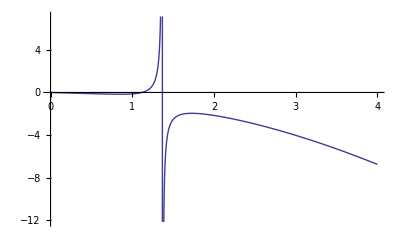

```mathematica
Plot[-((4 r^2-5) (4 r^2+5)^2 √(-25/((4 r^2+5)^2)+1))/(8 (2 r (r (4 r (3 r-4)+45)-35)-75)),{r,0,4}]
```

```mathematica
FS[(M-(2 a^2 M+q^2 r)/(a^2+r^2))/T0/.{rm->1,rp->2,a->Sqrt[5]/2,M->1,q->0,θ->π/2}]
```

-((4 r^2-5) (4 r^2+5)^2 √(25/((4 r^2+5)^2)-1))/(8 (2 r (r (4 r (3 r-4)+45)-35)-75))

```mathematica
-((4 r^2-5) (4 r^2+5)^2 √(25/((4 r^2+5)^2)-1))/(8 (2 r (r (4 r (3 r-4)+45)-35)-75))/.r->1.
```

0.-0.133631 ⅈ

## Γ & Ri

```mathematica
FS[Subscript[R, 2,3] Subscript[gi, 2,2] Subscript[gi, 3,3]/.->1/.{Δ[r]-> r^2-2M r+a^2, ρ[r,θ]-> √(r^2+a^2 Cos[θ]^2)}]
```

1/(4 (a^2 cos^2(θ)+r^2)^4)(Δ'(r) (a^2 cos(2 θ)+a^2+2 r^2) (√2 ρ^(0,1)(r,θ) √(a^2 cos(2 θ)+a^2+2 r^2)+a^2 sin(2 θ))-ρ^(1,0)(r,θ) (a^2 cos(2 θ)+a^2+2 r (r-2 M)) (4 ρ^(0,1)(r,θ) (a^2 cos^2(θ)+r^2)+√2 a^2 sin(2 θ) √(a^2 cos(2 θ)+a^2+2 r^2)))

```mathematica
FS[1/(4 (a^2 Cos[θ]^2+r^2)^4)(Δ'[r] (a^2 Cos[2 θ]+a^2+2 r^2) (√2 Derivative[0,1][ρ][r,θ] √(a^2 Cos[2 θ]+a^2+2 r^2)+a^2 Sin[2 θ])-Derivative[1,0][ρ][r,θ] (a^2 Cos[2 θ]+a^2+2 r (r-2 M)) (4 Derivative[0,1][ρ][r,θ] (a^2 Cos[θ]^2+r^2)+√2 a^2 Sin[2 θ] √(a^2 Cos[2 θ]+a^2+2 r^2)))/.{Δ'[r] ->2r-2M,Derivative[0,1][ρ][r,θ]-> -a^2 Sin[θ]Cos[θ]/√(r^2+a^2 Cos[θ]^2),Derivative[1,0][ρ][r,θ]->r/√(r^2+a^2 Cos[θ]^2)}]
```

0

## Gauss Bonnet Term calcs

```mathematica
Δ[r_]:=r^2-2M r+a^2+q^2; ρ[r_,θ_]:=√(r^2+a^2 Cos[θ]^2);
```

```mathematica
FS[Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2]/.->1]
```

-(8 q^2 (a^2+r (r-2 M)+q^2))/((a^2 cos(2 θ)+a^2+2 r^2)^3)

```mathematica
FS[Subscript[R, 3,3] Subscript[gi, 3,3] Subscript[gi, 3,3]/.->1]
```

(8 q^2)/((a^2 cos(2 θ)+a^2+2 r^2)^3)

```mathematica
FS[Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,0]/.->1]
```

(q^2 (a^2+r^2) (a^2 M cos(2 θ)+a^2 M+2 r (q^2-M r)))/(2 (a^2 cos^2(θ)+r^2)^5)

```mathematica
FS[Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,1]/.->1]
```

-(a q^2 sin^2(θ) (a^4 M+a^2 cos(2 θ) (a^2 M+r (q^2-M r))+3 a^2 r (q^2-M r)+2 r^3 (2 q^2-3 M r)))/(2 (a^2 cos^2(θ)+r^2)^5)

```mathematica
GBt1=FS[Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,0]/.->1]
```

-1/(4 (ρ(r,θ))^9)((ρ(r,θ))^2+a^2 sin^2(θ)) (2 ρ^(1,0)(r,θ) (a^2 sin^2(θ)-Δ(r))+Δ'(r) ρ(r,θ)) (2 (ρ^(1,0)(r,θ))^2 (Δ(r)-2 a^2 sin^2(θ))+Δ''(r) (ρ(r,θ))^2+2 ρ(r,θ) (-Δ'(r) ρ^(1,0)(r,θ)+Δ(r) ρ^(2,0)(r,θ)+ρ^(0,2)(r,θ)+cot(θ) ρ^(0,1)(r,θ))-2 (ρ^(0,1)(r,θ))^2)

```mathematica
GBϕ1=FS[Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,1]/.->1]
```

-1/(4 (ρ(r,θ))^9)a sin^2(θ) (Δ'(r) ρ(r,θ) ((ρ(r,θ))^2+a^2 sin^2(θ))+2 ρ^(1,0)(r,θ) (((ρ(r,θ))^2+a^2 sin^2(θ))^2-Δ(r) (2 (ρ(r,θ))^2+a^2 sin^2(θ)))) (2 ((ρ^(1,0)(r,θ))^2 (2 a^2 sin^2(θ)-Δ(r))+(ρ^(0,1)(r,θ))^2)-Δ''(r) (ρ(r,θ))^2-2 ρ(r,θ) (-Δ'(r) ρ^(1,0)(r,θ)+Δ(r) ρ^(2,0)(r,θ)+ρ^(0,2)(r,θ)+cot(θ) ρ^(0,1)(r,θ)))

```mathematica
GBt1=FS[Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,0]/.->1];
GB1=FS[Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,0]+a/(a^2+r^2)Subscript[R, 2,2] Subscript[gi, 2,2] Subscript[gi, 2,2] Subscript[Γ, 0,2,1]/.->1]
GBR2= FS[Table[(Subscript[R, j,k,2,0] Subscript[gi, 0,0]+Subscript[R, j,k,2,1] Subscript[gi, 1,0])Subscript[gi, 2,2]/.->1,{j,0,3},{k,0,3}]];
GBt2=FS[Sum[GBR2[[j+1,k+1]] Subscript[g, j,l] Subscript[gi, k,m](Γt[[l+1,m+1]]),{j,0,3},{k,0,3},{l,0,3},{m,0,3}]];
GB2=FS[Sum[GBR2[[j+1,k+1]] Subscript[g, j,l] Subscript[gi, k,m](Γt[[l+1,m+1]]+a/(a^2+r^2)Γϕ[[l+1,m+1]]),{j,0,3},{k,0,3},{l,0,3},{m,0,3}]];
```

0

Part::partd: Part specification TraditionalForm`Γt ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification TraditionalForm`Γt ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification TraditionalForm`Γt ⟦ 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
FS[GB1/.r-> M+Sqrt[M^2-a^2-q^2]]
```

(8 q^2 ((√(-a^2+M^2-q^2)+M) (q^2-M (√(-a^2+M^2-q^2)+M))+a^2 M))/(((√(-a^2+M^2-q^2)+M)^2+a^2) (a^2 cos(2 θ)+2 (√(-a^2+M^2-q^2)+M)^2+a^2)^3)

```mathematica
Subscript[x, 1]
```

ϕ

```mathematica
GBR2= FS[Table[(Subscript[R, j,k,2,0] Subscript[gi, 0,0]+Subscript[R, j,k,2,1] Subscript[gi, 1,0])Subscript[gi, 2,2]/.->1,{j,0,3},{k,0,3}]]
```

```mathematica
({{0, 0, (-Δ''(r) (ρ(r,θ))^6+2 (2 Δ'(r) Derivative[1,0][ρ](r,θ)+Δ(r) Derivative[2,0][ρ](r,θ)) (ρ(r,θ))^5+2 (-a^2 Δ''(r) sin^2(θ)+(Derivative[0,1][ρ](r,θ))^2+3 (a^2 sin^2(θ)-Δ(r)) (Derivative[1,0][ρ](r,θ))^2) (ρ(r,θ))^4+4 a^2 sin(θ) (cos(θ) Derivative[0,1][ρ](r,θ)+2 sin(θ) Δ'(r) Derivative[1,0][ρ](r,θ)) (ρ(r,θ))^3+a^2 sin^2(θ) (12 (a^2 sin^2(θ)-Δ(r)) (Derivative[1,0][ρ](r,θ))^2-a^2 sin^2(θ) Δ''(r)) (ρ(r,θ))^2+a^2 sin(θ) (2 cos(θ) (2 a^2 sin^2(θ)-Δ(r)) Derivative[0,1][ρ](r,θ)+sin(θ) ((4 a^2 sin^2(θ)+Δ(r)) Δ'(r) Derivative[1,0][ρ](r,θ)+2 Δ(r) (Δ(r)-a^2 sin^2(θ)) Derivative[2,0][ρ](r,θ))) ρ(r,θ)+2 a^2 sin^2(θ) (a^2 sin^2(θ)-Δ(r)) ((3 a^2 sin^2(θ)+Δ(r)) (Derivative[1,0][ρ](r,θ))^2-(Derivative[0,1][ρ](r,θ))^2))/(2 Δ(r) (ρ(r,θ))^6), (2 (Δ'(r) Derivative[0,1][ρ](r,θ)+Δ(r) Derivative[1,1][ρ](r,θ)) (ρ(r,θ))^6+(sin(2 θ) Δ'(r) a^2+2 (3 a^2 sin^2(θ)-4 Δ(r)) Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ)) (ρ(r,θ))^5+a^2 (5 Δ'(r) Derivative[0,1][ρ](r,θ) sin^2(θ)+2 (3 a^2 cos(θ) sin^3(θ)-4 sin(2 θ) Δ(r)) Derivative[1,0][ρ](r,θ)) (ρ(r,θ))^4+a^2 sin(θ) (cos(θ) (5 a^2 sin^2(θ)-3 Δ(r)) Δ'(r)+12 sin(θ) (a^2 sin^2(θ)-Δ(r)) Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ)) (ρ(r,θ))^3+a^2 (3 a^2 Δ'(r) Derivative[0,1][ρ](r,θ) sin^4(θ)+2 Δ(r) (Δ(r)-a^2 sin^2(θ)) Derivative[1,1][ρ](r,θ) sin^2(θ)+6 (2 a^4 cos(θ) sin^5(θ)-5 a^2 cos(θ) Δ(r) sin^3(θ)+sin(2 θ) (Δ(r))^2) Derivative[1,0][ρ](r,θ)) (ρ(r,θ))^2+a^2 sin^2(θ) (a^2 sin^2(θ)-Δ(r)) (3 cos(θ) sin(θ) Δ'(r) a^2+2 (3 a^2 sin^2(θ)+2 Δ(r)) Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ)) ρ(r,θ)+6 a^4 cos(θ) sin^3(θ) (Δ(r)-a^2 sin^2(θ))^2 Derivative[1,0][ρ](r,θ))/(2 Δ(r) (ρ(r,θ))^7)}, {0, 0, (a (-Δ''(r) (ρ(r,θ))^4+4 Δ'(r) Derivative[1,0][ρ](r,θ) (ρ(r,θ))^3-(a^2 Δ''(r) sin^2(θ)+6 (Δ(r)-a^2 sin^2(θ)) (Derivative[1,0][ρ](r,θ))^2) (ρ(r,θ))^2+(sin(2 θ) Derivative[0,1][ρ](r,θ) a^2+(4 a^2 sin^2(θ)+Δ(r)) Δ'(r) Derivative[1,0][ρ](r,θ)+2 Δ(r) (Δ(r)-a^2 sin^2(θ)) Derivative[2,0][ρ](r,θ)) ρ(r,θ)+2 (a^2 sin^2(θ)-Δ(r)) ((3 a^2 sin^2(θ)+Δ(r)) (Derivative[1,0][ρ](r,θ))^2-(Derivative[0,1][ρ](r,θ))^2)))/(2 Δ(r) (ρ(r,θ))^6), (a (2 (Δ'(r) Derivative[0,1][ρ](r,θ)-2 cot(θ) Δ(r) Derivative[1,0][ρ](r,θ)) (ρ(r,θ))^4+2 (a^2 sin^2(θ)-Δ(r)) (cot(θ) Δ'(r)+3 Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ)) (ρ(r,θ))^3+(3 a^2 Δ'(r) Derivative[0,1][ρ](r,θ) sin^2(θ)+2 (3 cos(θ) sin^3(θ) a^4-5 sin(2 θ) Δ(r) a^2+4 cot(θ) (Δ(r))^2) Derivative[1,0][ρ](r,θ)+2 Δ(r) (Δ(r)-a^2 sin^2(θ)) Derivative[1,1][ρ](r,θ)) (ρ(r,θ))^2+(a^2 sin^2(θ)-Δ(r)) (3 cos(θ) sin(θ) Δ'(r) a^2+2 (3 a^2 sin^2(θ)+2 Δ(r)) Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ)) ρ(r,θ)+3 sin(2 θ) (a^3 sin^2(θ)-a Δ(r))^2 Derivative[1,0][ρ](r,θ)))/(2 Δ(r) (ρ(r,θ))^7)}, {(-2 a^2 (a^2 sin^2(θ)+(ρ(r,θ))^2) Derivative[0,1][ρ](r,θ) (cos(θ) sin(θ) a^2+ρ(r,θ) Derivative[0,1][ρ](r,θ)) sin^2(θ)+Δ(r) (-Δ''(r) (ρ(r,θ))^5+(4 Δ'(r) Derivative[1,0][ρ](r,θ)-2 a^2 sin^2(θ) Derivative[2,0][ρ](r,θ)) (ρ(r,θ))^4+(2 (Derivative[0,1][ρ](r,θ))^2-a^2 sin^2(θ) (Δ''(r)-6 (Derivative[1,0][ρ](r,θ))^2)) (ρ(r,θ))^3+a^2 sin(θ) (-2 a^2 Derivative[2,0][ρ](r,θ) sin^3(θ)+5 Δ'(r) Derivative[1,0][ρ](r,θ) sin(θ)+4 cos(θ) Derivative[0,1][ρ](r,θ)) (ρ(r,θ))^2+2 a^2 sin^2(θ) ((Derivative[0,1][ρ](r,θ))^2+4 a^2 sin^2(θ) (Derivative[1,0][ρ](r,θ))^2) ρ(r,θ)+4 a^4 cos(θ) sin^3(θ) Derivative[0,1][ρ](r,θ))+2 (Δ(r))^2 (ρ(r,θ) (ρ(r,θ) (a^2 sin^2(θ)+(ρ(r,θ))^2) Derivative[2,0][ρ](r,θ)-(4 a^2 sin^2(θ)+3 (ρ(r,θ))^2) (Derivative[1,0][ρ](r,θ))^2)-a^2 cos(θ) sin(θ) Derivative[0,1][ρ](r,θ)))/(2 (ρ(r,θ))^9), (a sin^2(θ) ((sin(2 θ) Derivative[0,1][ρ](r,θ) a^2+8 ρ(r,θ) (a^2 sin^2(θ)+(ρ(r,θ))^2) (Derivative[1,0][ρ](r,θ))^2-2 (ρ(r,θ))^2 (a^2 sin^2(θ)+2 (ρ(r,θ))^2) Derivative[2,0][ρ](r,θ)) (Δ(r))^2+(2 Derivative[2,0][ρ](r,θ) (ρ(r,θ))^6+Δ''(r) (ρ(r,θ))^5+(4 a^2 sin^2(θ) Derivative[2,0][ρ](r,θ)-5 Δ'(r) Derivative[1,0][ρ](r,θ)) (ρ(r,θ))^4+(a^2 sin^2(θ) (Δ''(r)-8 (Derivative[1,0][ρ](r,θ))^2)-4 (Derivative[0,1][ρ](r,θ))^2) (ρ(r,θ))^3+a^2 sin(θ) (2 a^2 Derivative[2,0][ρ](r,θ) sin^3(θ)-5 Δ'(r) Derivative[1,0][ρ](r,θ) sin(θ)-6 cos(θ) Derivative[0,1][ρ](r,θ)) (ρ(r,θ))^2-2 a^2 sin^2(θ) ((Derivative[0,1][ρ](r,θ))^2+4 a^2 sin^2(θ) (Derivative[1,0][ρ](r,θ))^2) ρ(r,θ)-4 a^4 cos(θ) sin^3(θ) Derivative[0,1][ρ](r,θ)) Δ(r)+(a^2 sin^2(θ)+(ρ(r,θ))^2)^2 Derivative[0,1][ρ](r,θ) (sin(2 θ) a^2+2 ρ(r,θ) Derivative[0,1][ρ](r,θ))))/(2 (ρ(r,θ))^9), 0, 0}, {(2 (-2 cos(θ) sin(θ) Derivative[1,0][ρ](r,θ) a^2+Δ'(r) Derivative[0,1][ρ](r,θ)+(Δ(r)-a^2 sin^2(θ)) Derivative[1,1][ρ](r,θ)) (ρ(r,θ))^4+8 (a^2 sin^2(θ)-Δ(r)) Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ) (ρ(r,θ))^3+a^2 sin(θ) (3 sin(θ) Δ'(r) Derivative[0,1][ρ](r,θ)-2 cos(θ) (a^2 sin^2(θ)+2 Δ(r)) Derivative[1,0][ρ](r,θ)+2 sin(θ) (Δ(r)-a^2 sin^2(θ)) Derivative[1,1][ρ](r,θ)) (ρ(r,θ))^2+a^2 sin(θ) (a^2 sin^2(θ)-Δ(r)) (cos(θ) Δ'(r)+10 sin(θ) Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ)) ρ(r,θ)+2 sin(2 θ) (a^3 sin^2(θ)-a Δ(r))^2 Derivative[1,0][ρ](r,θ))/(2 (ρ(r,θ))^9), -(a sin(θ) (-2 (2 cos(θ) Derivative[1,0][ρ](r,θ)+sin(θ) Derivative[1,1][ρ](r,θ)) (ρ(r,θ))^6+(2 sin(θ) Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ)-2 cos(θ) Δ'(r)) (ρ(r,θ))^5+(2 sin(θ) Δ'(r) Derivative[0,1][ρ](r,θ)+4 cos(θ) (2 Δ(r)-3 a^2 sin^2(θ)) Derivative[1,0][ρ](r,θ)+4 sin(θ) (Δ(r)-a^2 sin^2(θ)) Derivative[1,1][ρ](r,θ)) (ρ(r,θ))^4-2 sin(θ) (cos(θ) sin(θ) Δ'(r) a^2+6 (Δ(r)-a^2 sin^2(θ)) Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ)) (ρ(r,θ))^3+a^2 sin^2(θ) (3 sin(θ) Δ'(r) Derivative[0,1][ρ](r,θ)-2 cos(θ) (2 a^2 sin^2(θ)+Δ(r)) Derivative[1,0][ρ](r,θ)+2 sin(θ) (Δ(r)-a^2 sin^2(θ)) Derivative[1,1][ρ](r,θ)) (ρ(r,θ))^2+a^2 sin^2(θ) (a^2 sin^2(θ)-Δ(r)) (cos(θ) Δ'(r)+10 sin(θ) Derivative[0,1][ρ](r,θ) Derivative[1,0][ρ](r,θ)) ρ(r,θ)+4 cos(θ) (a^3 sin^3(θ)-a sin(θ) Δ(r))^2 Derivative[1,0][ρ](r,θ)))/(2 (ρ(r,θ))^9), 0, 0}})
```

(0 | 0 | ((5 q^2-27 M r) a^6+(q^4-r (5 M+19 r) q^2+M (6 M-31 r) r^2) a^4-(q^2-3 M r) (a^2+q^2+r^2-2 M r) cos(4 θ) a^4-4 r^2 (q^4+3 r (4 r-M) q^2+M (2 M-3 r) r^2) a^2+4 ((q^2-6 M r) a^4+r^2 (3 q^2-13 M r) a^2+r^2 (q^4+r (2 r-3 M) q^2+M (2 M-7 r) r^2)) cos(2 θ) a^2+8 r^6 (2 M r-3 q^2))/(8 (a^2+q^2+r (r-2 M)) (r^2+a^2 cos^2(θ))^4) | (3 a^2 (a^2+r^2) (M a^2+M cos(2 θ) a^2-6 M r^2+4 q^2 r) sin(2 θ))/(4 (r^2+a^2 cos^2(θ))^4)
0 | 0 | (a ((2 q^2-9 M r) a^4+(q^4-r (5 M+6 r) q^2+3 M (2 M-r) r^2) a^2+(q^4+r (2 r-5 M) q^2+3 M (2 M-3 r) r^2+a^2 (2 q^2-9 M r)) cos(2 θ) a^2-2 r^2 (q^4+r (4 r-3 M) q^2+M (2 M-3 r) r^2)))/(2 (a^2+q^2+r (r-2 M)) (r^2+a^2 cos^2(θ))^4) | -(a (cos(2 θ) a^2-5 a^2-4 r^2) (M a^2+M cos(2 θ) a^2-6 M r^2+4 q^2 r) cot(θ))/(4 (r^2+a^2 cos^2(θ))^4)
-((a^2+q^2+r (r-2 M)) ((27 M r-5 q^2) a^4+(q^2-3 M r) cos(4 θ) a^4+4 r^2 (6 q^2+M r) a^2-4 ((q^2-6 M r) a^2+r^2 (2 q^2-7 M r)) cos(2 θ) a^2+8 r^4 (3 q^2-2 M r)))/(8 (r^2+a^2 cos^2(θ))^5) | (a (a^2+r^2) (a^2+q^2+r (r-2 M)) ((9 M r-2 q^2) a^2+(9 M r-2 q^2) cos(2 θ) a^2+2 r^2 (4 q^2-3 M r)) sin^2(θ))/(2 (r^2+a^2 cos^2(θ))^5) | 0 | 0
(a^2 (3 a^2+q^2+r (3 r-2 M)) (M a^2+M cos(2 θ) a^2-6 M r^2+4 q^2 r) sin(2 θ))/(4 (r^2+a^2 cos^2(θ))^5) | (a (M (a^2+q^2+r^2-2 M r) sin(6 θ) a^4-4 (2 M a^4+5 M r^4-2 (3 M^2+q^2) r^3+7 M (a^2+q^2) r^2-2 q^2 (a^2+q^2) r) sin(4 θ) a^2-(19 M a^6+(-6 r M^2+3 q^2 M-85 r^2 M+80 q^2 r) a^4+8 r (2 q^4+r (18 r-7 M) q^2+M (6 M-25 r) r^2) a^2+32 r^5 (2 q^2-3 M r)) sin(2 θ)))/(32 (r^2+a^2 cos^2(θ))^5) | 0 | 0)

```mathematica
Subscript[gi, 1,0]
```

-(csc^2(θ) ((a sin^2(θ) (a^2 cos^2(θ)+r^2)^2)/(a^2-2 M r+q^2+r^2)-a sin^2(θ) (a^2 cos^2(θ)+r^2)+(a^3 sin^4(θ) (a^2 cos^2(θ)+r^2))/(a^2-2 M r+q^2+r^2)))/((a^2 cos^2(θ)+r^2)^2)

```mathematica
Subscript[gi, 0,0] Subscript[Γ, 0,0,0]/.l->1
```

0

```mathematica
Γt
```

Γt

```mathematica
GB20=FS[Sum[GBR2[[k+1,j+1]](Γt[[j+1,k+1]]+a/(a^2+r^2)Γϕ[[j+1,k+1]]),{j,0,3},{k,0,3}]]
```

1/((a^2+r^2) (a^2 cos(2 θ)+a^2+2 r^2)^5)8 (-5 a^8 M+a^6 (22 M^2 r-7 M q^2+39 M r^2-24 q^2 r)+2 a^4 r (3 q^2 r (19 M-4 r)+14 M r^2 (2 r-3 M)-13 q^4)+4 a^2 r^3 (11 M q^2 r+M r^2 (3 r-14 M)+2 q^4)+a^2 cos(2 θ) (-9 a^6 M+a^4 (42 M^2 r-13 M q^2+7 M r^2-16 q^2 r)+4 a^2 r (3 q^2 r (7 M-4 r)+M r^2 (13 r-10 M)-5 q^4)+a^2 cos(2 θ) (-3 a^4 M+a^2 (18 M^2 r-5 M q^2-31 M r^2+8 q^2 r)+a^2 M cos(2 θ) (a^2-2 M r+q^2+r^2)+2 r (q^2 r (4 r-15 M)+2 M r^2 (11 M-7 r)+3 q^4))+4 r^3 (q^2 r (27 M-8 r)+M r^2 (9 r-22 M)-6 q^4))+8 r^5 (3 q^2-2 M r) (q^2-M r))

```mathematica
GBt2=FS[Sum[GBR2[[j+1,k+1]] Subscript[g, j,l] Subscript[gi, k,m](Γt[[l+1,m+1]]),{j,0,3},{k,0,3},{l,0,3},{m,0,3}]]
```

1/(16 Δ(r) (ρ(r,θ))^11)(8 Δ(r) Δ'(r) Δ''(r) (ρ(r,θ))^7-8 Δ(r) (-2 sin(2 θ) ρ^(1,1)(r,θ) a^2+(-8 a^2 cos^2(θ)+4 (Δ'(r))^2+2 (Δ(r)-a^2 sin^2(θ)) Δ''(r)) ρ^(1,0)(r,θ)+2 Δ(r) Δ'(r) ρ^(2,0)(r,θ)) (ρ(r,θ))^6+4 (8 ρ^(1,0)(r,θ) ρ^(2,0)(r,θ) (Δ(r))^3+4 (-2 a^2 ρ^(1,0)(r,θ) ρ^(2,0)(r,θ) sin^2(θ)+7 Δ'(r) (ρ^(1,0)(r,θ))^2+2 ρ^(0,1)(r,θ) ρ^(1,1)(r,θ)) (Δ(r))^2+2 (Δ'(r) (a^2 (Δ''(r)-14 (ρ^(1,0)(r,θ))^2) sin^2(θ)+2 (2 a^2 cos^2(θ)+(ρ^(0,1)(r,θ))^2))-4 a^2 sin(θ) ρ^(0,1)(r,θ) (cos(θ) ρ^(1,0)(r,θ)+sin(θ) ρ^(1,1)(r,θ))) Δ(r)-8 a^2 sin^2(θ) Δ'(r) (ρ^(0,1)(r,θ))^2) (ρ(r,θ))^5-2 (-8 sin(2 θ) (Δ(r)-2 a^2 sin^2(θ)) Δ'(r) ρ^(0,1)(r,θ) a^2+16 sin^2(θ) Δ(r) (Δ'(r))^2 ρ^(1,0)(r,θ) a^2+4 (2 Δ(r)-2 a^2 sin^2(θ)) (sin(2 θ) Δ(r) ρ^(1,1)(r,θ) a^2+ρ^(1,0)(r,θ) (-6 a^2 sin^2(θ) (ρ^(0,1)(r,θ))^2+6 (Δ(r))^2 (ρ^(1,0)(r,θ))^2+Δ(r) (a^2 (Δ''(r)-6 (ρ^(1,0)(r,θ))^2) sin^2(θ)+6 (2 a^2 cos^2(θ)+(ρ^(0,1)(r,θ))^2))))) (ρ(r,θ))^4-16 a^2 (7 sin^2(θ) (a^2 sin^2(θ)-Δ(r)) Δ(r) Δ'(r) (ρ^(1,0)(r,θ))^2+sin(2 θ) (6 a^4 sin^4(θ)-11 a^2 Δ(r) sin^2(θ)+5 (Δ(r))^2) ρ^(0,1)(r,θ) ρ^(1,0)(r,θ)+Δ'(r) (2 (a^4 sin^4(θ)-3 a^2 Δ(r) sin^2(θ)+(Δ(r))^2) cos^2(θ)+3 sin^2(θ) (a^2 sin^2(θ)-Δ(r)) (ρ^(0,1)(r,θ))^2)) (ρ(r,θ))^3+8 a^2 (2 Δ(r)-2 a^2 sin^2(θ)) (6 a^2 cos(θ) Δ'(r) ρ^(0,1)(r,θ) sin^3(θ)+6 (a^2 sin^2(θ)-Δ(r)) Δ(r) (ρ^(1,0)(r,θ))^3 sin^2(θ)+(2 (3 a^4 sin^4(θ)-11 a^2 Δ(r) sin^2(θ)+4 (Δ(r))^2) cos^2(θ)+6 sin^2(θ) (a^2 sin^2(θ)-Δ(r)) (ρ^(0,1)(r,θ))^2) ρ^(1,0)(r,θ)+sin(2 θ) Δ(r) (Δ(r)-a^2 sin^2(θ)) ρ^(1,1)(r,θ)) (ρ(r,θ))^2-sin(2 θ) (2 a^3 sin^2(θ)-2 a Δ(r))^2 (3 sin(2 θ) Δ'(r) a^2+4 (6 a^2 sin^2(θ)+Δ(r)) ρ^(0,1)(r,θ) ρ^(1,0)(r,θ)) ρ(r,θ)+3 a^4 sin^2(2 θ) (2 Δ(r)-2 a^2 sin^2(θ))^3 ρ^(1,0)(r,θ))

```mathematica
GB2=FS[Sum[GBR2[[j+1,k+1]] Subscript[g, j,l] Subscript[gi, k,m](Γϕ[[l+1,m+1]]),{j,0,3},{k,0,3},{l,0,3},{m,0,3}]]
```

1/(2 Δ(r) (ρ(r,θ))^11)a (-2 Δ(r) ((4 cos^2(θ)+sin^2(θ) Δ''(r)) ρ^(1,0)(r,θ)+sin(2 θ) ρ^(1,1)(r,θ)) (ρ(r,θ))^8-(Δ(r) (2 sin(2 θ) ρ^(0,1)(r,θ) ρ^(1,0)(r,θ)+Δ'(r) (4 cos^2(θ)+sin^2(θ) (Δ''(r)-8 (ρ^(1,0)(r,θ))^2)))-4 sin^2(θ) Δ'(r) (ρ^(0,1)(r,θ))^2) (ρ(r,θ))^7+(4 Δ(r) (Δ'(r))^2 ρ^(1,0)(r,θ) sin^2(θ)+2 Δ'(r) (2 sin(2 θ) ρ^(0,1)(r,θ) a^2+(Δ(r))^2 ρ^(2,0)(r,θ)) sin^2(θ)+ρ^(1,0)(r,θ) (12 a^2 (ρ^(0,1)(r,θ))^2 sin^4(θ)+2 (Δ(r))^2 (8 cos^2(θ)+sin^2(θ) (Δ''(r)-6 (ρ^(1,0)(r,θ))^2))+Δ(r) (-4 a^2 Δ''(r) sin^4(θ)-12 (ρ^(0,1)(r,θ))^2 sin^2(θ)+a^2 (12 (ρ^(1,0)(r,θ))^2 sin^4(θ)+5 cos(4 θ)-5)))+4 Δ(r) (sin(2 θ) Δ(r)-3 a^2 cos(θ) sin^3(θ)) ρ^(1,1)(r,θ)) (ρ(r,θ))^6+(2 sin^2(θ) (11 a^2 sin^2(θ)-6 Δ(r)) Δ(r) Δ'(r) (ρ^(1,0)(r,θ))^2+4 (6 a^4 cos(θ) sin^5(θ)-Δ(r) (5 a^2 cos(θ) sin^3(θ)+sin(2 θ) Δ(r))) ρ^(0,1)(r,θ) ρ^(1,0)(r,θ)+Δ'(r) (4 a^4 cos^2(θ) sin^4(θ)-2 (Δ(r)-5 a^2 sin^2(θ)) (ρ^(0,1)(r,θ))^2 sin^2(θ)-a^2 Δ(r) (Δ''(r) sin^4(θ)+3 sin^2(2 θ)))) (ρ(r,θ))^5+(4 a^2 Δ(r) (Δ'(r))^2 ρ^(1,0)(r,θ) sin^4(θ)+4 a^2 cos(θ) (5 a^2 sin^2(θ)-Δ(r)) Δ'(r) ρ^(0,1)(r,θ) sin^3(θ)+12 a^2 cos(θ) Δ(r) (Δ(r)-a^2 sin^2(θ)) ρ^(1,1)(r,θ) sin^3(θ)+8 Δ(r) (3 a^4 sin^4(θ)-4 a^2 Δ(r) sin^2(θ)+(Δ(r))^2) (ρ^(1,0)(r,θ))^3 sin^2(θ)+(12 a^6 cos^2(θ) sin^6(θ)+8 (3 a^4 sin^4(θ)-4 a^2 Δ(r) sin^2(θ)+(Δ(r))^2) (ρ^(0,1)(r,θ))^2 sin^2(θ)+a^2 Δ(r) (2 (Δ(r)-a^2 sin^2(θ)) Δ''(r) sin^4(θ)+9 sin^2(2 θ) (Δ(r)-2 a^2 sin^2(θ)))) ρ^(1,0)(r,θ)) (ρ(r,θ))^4+2 a^2 sin^2(θ) (7 sin^2(θ) (a^2 sin^2(θ)-Δ(r)) Δ(r) Δ'(r) (ρ^(1,0)(r,θ))^2+sin(2 θ) (12 a^4 sin^4(θ)-13 a^2 Δ(r) sin^2(θ)+(Δ(r))^2) ρ^(0,1)(r,θ) ρ^(1,0)(r,θ)+Δ'(r) ((5 a^4 sin^4(θ)-8 a^2 Δ(r) sin^2(θ)+(Δ(r))^2) cos^2(θ)+3 sin^2(θ) (a^2 sin^2(θ)-Δ(r)) (ρ^(0,1)(r,θ))^2)) (ρ(r,θ))^3+a^2 (12 a^2 cos(θ) (a^2 sin^2(θ)-Δ(r)) Δ'(r) ρ^(0,1)(r,θ) sin^5(θ)+12 Δ(r) (Δ(r)-a^2 sin^2(θ))^2 (ρ^(1,0)(r,θ))^3 sin^4(θ)-4 cos(θ) Δ(r) (Δ(r)-a^2 sin^2(θ))^2 ρ^(1,1)(r,θ) sin^3(θ)+(24 a^6 cos^2(θ) sin^8(θ)+12 (Δ(r)-a^2 sin^2(θ))^2 (ρ^(0,1)(r,θ))^2 sin^4(θ)+Δ(r) (-72 a^4 cos^2(θ) sin^6(θ)+56 a^2 cos^2(θ) Δ(r) sin^4(θ)+(cos(4 θ)-1) (Δ(r))^2)) ρ^(1,0)(r,θ)) (ρ(r,θ))^2+2 a^2 cos(θ) sin^3(θ) (Δ(r)-a^2 sin^2(θ))^2 (3 cos(θ) sin(θ) Δ'(r) a^2+2 (6 a^2 sin^2(θ)+Δ(r)) ρ^(0,1)(r,θ) ρ^(1,0)(r,θ)) ρ(r,θ)+12 a^4 cos^2(θ) sin^4(θ) (a^2 sin^2(θ)-Δ(r))^3 ρ^(1,0)(r,θ))

```mathematica
GBϕ2=GB2;
```

```mathematica
GB2=FS[Sum[GBR2[[j+1,k+1]] Subscript[g, j,l] Subscript[gi, k,m](Γt[[l+1,m+1]]+a/(a^2+r^2)Γϕ[[l+1,m+1]]),{j,0,3},{k,0,3},{l,0,3},{m,0,3}]]
```

1/((a^2+r^2) (a^2 cos(2 θ)+a^2+2 r^2)^5)8 (5 a^8 M+a^6 (-22 M^2 r+7 M q^2-39 M r^2+24 q^2 r)+2 a^4 r (3 q^2 r (4 r-19 M)+14 M r^2 (3 M-2 r)+13 q^4)-4 a^2 r^3 (11 M q^2 r+M r^2 (3 r-14 M)+2 q^4)+a^2 cos(2 θ) (9 a^6 M+a^4 (-42 M^2 r+13 M q^2-7 M r^2+16 q^2 r)+4 a^2 r (3 q^2 r (4 r-7 M)+M r^2 (10 M-13 r)+5 q^4)+a^2 cos(2 θ) (3 a^4 M+a^2 (-18 M^2 r+5 M q^2+31 M r^2-8 q^2 r)-a^2 M cos(2 θ) (a^2+r (r-2 M)+q^2)+2 r (q^2 r (15 M-4 r)+2 M r^2 (7 r-11 M)-3 q^4))+4 r^3 (q^2 r (8 r-27 M)+M r^2 (22 M-9 r)+6 q^4))-8 r^5 (3 q^2-2 M r) (q^2-M r))

```mathematica
GB1/.{q->q,a->0}
```

(q^2 (q^2-M r))/r^7

```mathematica
GB0=FS[(α GB1+GB20)Sin[θ] ρ[r,θ]^2]
```

1/((a^2+r^2) (a^2 cos(2 θ)+a^2+2 r^2)^5)8 sin(θ) (a^2 cos^2(θ)+r^2) (-5 a^8 M+a^6 (22 M^2 r+M ((α-7) q^2+39 r^2)-24 q^2 r)+a^4 r (3 q^2 r ((α+38) M-8 r)+28 M r^2 (2 r-3 M)+(α-26) q^4)+4 a^2 r^3 (11 M q^2 r+M r^2 (3 r-14 M)+(α+2) q^4)+a^2 cos(2 θ) (-9 a^6 M+a^4 (42 M^2 r+M ((2 α-13) q^2+7 r^2)-16 q^2 r)+2 a^2 r (q^2 r ((α+42) M-24 r)+2 M r^2 (13 r-10 M)+(α-10) q^4)+a^2 cos(2 θ) (-3 a^4 M+a^2 (18 M^2 r+M ((α-5) q^2-31 r^2)+8 q^2 r)+a^2 M cos(2 θ) (a^2-2 M r+q^2+r^2)+r (q^2 r (8 r-(α+30) M)+4 M r^2 (11 M-7 r)+(α+6) q^4))+4 r^3 (-q^2 r ((α-27) M+8 r)+M r^2 (9 r-22 M)+(α-6) q^4))+4 r^5 (q^2-M r) ((α+6) q^2-4 M r))

```mathematica
Δ[r_]:=r^2-2M r+a^2+q^2; ρ[r_,θ_]:=√(r^2+a^2 Cos[θ]^2);
```

```mathematica
Clear[Δ,ρ]
```

```mathematica
GBt=FS[(4 GBt1+GBt2)Sin[θ] ρ[r,θ]^2]
```

1/((a^2 cos(2 θ)+a^2+2 r^2)^5)8 (a^2+r^2) sin(θ) (q^2-2 M r) (5 a^4 M cos(4 θ)+15 a^4 M+4 a^2 cos(2 θ) (5 M (a^2-2 r^2)+7 q^2 r)+4 a^2 r (7 q^2-10 M r)+8 r^3 (M r-q^2))

1/((a^2 cos(2 θ)+a^2+2 r^2)^5)8 (a^2+r^2) sin(θ) (q^2-2 M r) (5 a^4 M cos(4 θ)+15 a^4 M+4 a^2 cos(2 θ) (5 M (a^2-2 r^2)+7 q^2 r)+4 a^2 r (7 q^2-10 M r)+8 r^3 (M r-q^2))

```mathematica
GBϕ=FS[(4 GBϕ1+GBϕ2)Sin[θ] ρ[r,θ]^2]
```

1/(4 (a^2 cos(2 θ)+a^2+2 r^2)^5)a (a^6 (-M) sin(9 θ) (a^2-2 M r+q^2+r^2)+a^4 sin(7 θ) (5 a^4 M+a^2 (-34 M^2 r+17 M q^2+57 M r^2-16 q^2 r)+4 r (4 q^2 r (3 M-r)+M r^2 (13 r-20 M)-q^4))+4 a^2 sin(5 θ) (10 a^6 M+a^4 (-10 M^2 r+5 M (q^2+3 r^2)+12 q^2 r)+a^2 r (28 q^2 r (r-3 M)+5 M r^2 (12 M+5 r)+27 q^4)+4 r^3 (q^2 r (4 r-23 M)+5 M r^2 (2 M+r)+9 q^4))+2 sin(θ) (23 a^8 M+a^6 (54 M^2 r-3 M (9 q^2+29 r^2)+88 q^2 r)-2 a^4 r (-4 q^2 r (39 M+35 r)+5 M r^2 (20 M+51 r)+53 q^4)-16 a^2 r^3 (q^2 r (4 r-5 M)+M r^2 (19 r-2 M)+3 q^4)+32 r^5 (4 q^2 r (3 M-2 r)+3 M r^3-6 q^4))+4 sin(3 θ) (20 a^8 M+a^6 (26 M^2 r-13 M q^2-43 M r^2+60 q^2 r)+a^4 r (4 q^2 r (15 M+43 r)-M r^2 (20 M+243 r)-25 q^4)-4 a^2 r^3 (-5 q^2 r (7 M+12 r)+9 M r^2 (2 M+9 r)+13 q^4)-16 r^5 (4 q^2 r (M-2 r)+9 M r^3-2 q^4)))

```mathematica
GB=FS[(α GB1+GB2)Sin[θ] ρ[r,θ]^2]
```

1/((a^2+r^2) (a^2 cos(2 θ)+a^2+2 r^2)^5)8 sin(θ) (a^2 cos^2(θ)+r^2) (5 a^8 M+a^6 (-22 M^2 r+M ((α+7) q^2-39 r^2)+24 q^2 r)+a^4 r (3 q^2 r ((α-38) M+8 r)+28 M r^2 (3 M-2 r)+(α+26) q^4)+4 a^2 r^3 (-11 M q^2 r+M r^2 (14 M-3 r)+(α-2) q^4)+a^2 cos(2 θ) (9 a^6 M+a^4 (-42 M^2 r+M ((2 α+13) q^2-7 r^2)+16 q^2 r)+2 a^2 r (q^2 r ((α-42) M+24 r)+2 M r^2 (10 M-13 r)+(α+10) q^4)+a^2 cos(2 θ) (3 a^4 M+a^2 (-18 M^2 r+M ((α+5) q^2+31 r^2)-8 q^2 r)-a^2 M cos(2 θ) (a^2-2 M r+q^2+r^2)+r (-q^2 r ((α-30) M+8 r)+4 M r^2 (7 r-11 M)+(α-6) q^4))+4 r^3 (q^2 r (8 r-(α+27) M)+M r^2 (22 M-9 r)+(α+6) q^4))-4 r^5 (M r-q^2) (4 M r+(α-6) q^2))

```mathematica
GBI0=Assuming[r>0&&a>0,Integrate[GB0,{θ,0,π}]]
```

1/(2 a r^4 (a^2+r^2)^3)ⅈ (q^2 (a^2+r^2)^2 log(r-ⅈ a) (3 a^4+a^2 (r ((α-2) M+2 r)+3 q^2)-r^2 (r ((α+2) M+r)-(α+3) q^2))-q^2 (a^2+r^2)^2 log(r+ⅈ a) (3 a^4+a^2 (r ((α-2) M+2 r)+3 q^2)-r^2 (r ((α+2) M+r)-(α+3) q^2))-2 ⅈ a r (3 a^6 q^2+a^4 q^2 (r ((α-2) M+7 r)+3 q^2)+a^2 r^2 (-8 M^2 r^2+q^2 r (5 r-4 M)+(α+8) q^4)+r^4 (8 M^2 r^2+q^2 r (r-(α+18) M)+(α+9) q^4)))

```mathematica
GBIt=Assuming[r>0&&a>0,Integrate[GBt,{θ,0,π}]]
```

-(4 (q^2-2 M r) (a^2 M+r (q^2-M r)))/((a^2+r^2)^3)

```mathematica
Limit[GBIt,r->∞]
```

0

```mathematica
FS[Subscript[R, 2,0,2,0]/.{l->1,q->0,a->0}]
```

-(M ( M-5 M+2 r))/r^4

```mathematica
GBIϕ=Assuming[r>0&&a>0,Integrate[GBϕ,{θ,0,π}]]
```

-(q^2 (a r (3 a^2+r^2)+(3 a^2-r^2) (a^2+r^2) tan^-1(a/r)) (a^2+r (r-2 M)+q^2))/(a^2 r^4 (a^2+r^2))

```mathematica
FS[{GBIt/Sqrt[M^2-a^2-q^2],r^2+a^2+q^2}/.r-> M+Sqrt[M^2-a^2-q^2]]
```

{4/(q^2-2 M (√(-a^2+M^2-q^2)+M)),2 M (√(-a^2+M^2-q^2)+M)}

```mathematica
FS[GBIϕ/.r-> M+Sqrt[M^2-a^2-q^2]]
```

0

```mathematica
Limit[GBIϕ,r->∞]
```

0

```mathematica
GBI=Assuming[r>0&&a>0,Integrate[GB,{θ,0,π}]]
```

-1/(2 a r^4 (a^2+r^2)^3)ⅈ (q^2 (a^2+r^2)^2 log(r-ⅈ a) (3 a^4+a^2 (r (2 r-(α+2) M)+3 q^2)-r^2 (r (-α M+2 M+r)+(α-3) q^2))-q^2 (a^2+r^2)^2 log(r+ⅈ a) (3 a^4+a^2 (r (2 r-(α+2) M)+3 q^2)-r^2 (r (-α M+2 M+r)+(α-3) q^2))-2 ⅈ a r (3 a^6 q^2+a^4 q^2 (r (7 r-(α+2) M)+3 q^2)-a^2 r^2 (8 M^2 r^2+q^2 r (4 M-5 r)+(α-8) q^4)+r^4 (8 M^2 r^2+q^2 r ((α-18) M+r)-(α-9) q^4)))

```mathematica
GBI0=FS[GBI0]
```

1/(2 a r^4 (a^2+r^2)^3)ⅈ (q^2 (a^2+r^2)^2 (log(r-ⅈ a)-log(r+ⅈ a)) ((a^2+r^2) (3 a^2-r (2 M+r)+3 q^2)+α r (a^2 M+r (q^2-M r)))-2 ⅈ a r (3 a^6 q^2+a^4 q^2 (r ((α-2) M+7 r)+3 q^2)+a^2 r^2 (-8 M^2 r^2+q^2 r (5 r-4 M)+(α+8) q^4)+r^4 (8 M^2 r^2+q^2 r (r-(α+18) M)+(α+9) q^4)))

```mathematica
GBI=FS[GBI]
```

-1/(2 a r^4 (a^2+r^2)^3)ⅈ (q^2 (a^2+r^2)^2 (log(r-ⅈ a)-log(r+ⅈ a)) ((a^2+r^2) (3 a^2-r (2 M+r)+3 q^2)+α r (r (M r-q^2)-a^2 M))-2 ⅈ a r (3 a^6 q^2+a^4 q^2 (r (7 r-(α+2) M)+3 q^2)+a^2 r^2 (-8 M^2 r^2+q^2 r (5 r-4 M)-(α-8) q^4)+r^4 (8 M^2 r^2+q^2 r ((α-18) M+r)-(α-9) q^4)))

```mathematica
FS[GBI0/.α->4]
```

1/(2 a r^4 (a^2+r^2)^3)ⅈ (q^2 (a^2+r^2)^2 (log(r-ⅈ a)-log(r+ⅈ a)) (3 a^4+a^2 (2 r (M+r)+3 q^2)-r^2 (r (6 M+r)-7 q^2))-2 ⅈ a r (3 a^6 q^2+a^4 q^2 (r (2 M+7 r)+3 q^2)+a^2 r^2 (-8 M^2 r^2+q^2 r (5 r-4 M)+12 q^4)+r^4 (8 M^2 r^2+q^2 r (r-22 M)+13 q^4)))

```mathematica
FS[(a^2+r^2) (3 a^2-r (2 M+r)+3 q^2)+α r (r (M r-q^2)-a^2 M)/.α->3]
```

3 a^4+a^2 (r (2 r-5 M)+3 q^2)+r^3 (M-r)

```mathematica
FS[GBI0/.->1/.α->4/.{r-> M+Sqrt[M^2-a^2-q^2]}]
```

(ⅈ (-8 q^2 (-3 M q^2 √(-a^2+M^2-q^2)+a^2 (q^2-2 M (√(-a^2+M^2-q^2)+2 M))+4 M^3 √(-a^2+M^2-q^2)+4 M^4-5 M^2 q^2+q^4) (q^2-2 M (√(-a^2+M^2-q^2)+M))^2 (log(√(-a^2+M^2-q^2)-ⅈ a+M)-log(√(-a^2+M^2-q^2)+ⅈ a+M))-2 ⅈ a (√(-a^2+M^2-q^2)+M) (3 a^6 q^2+(√(-a^2+M^2-q^2)+M)^4 (-q^2 (20 M (√(-a^2+M^2-q^2)+M)+a^2+q^2)+8 M^2 (√(-a^2+M^2-q^2)+M)^2+13 q^4)+a^2 (√(-a^2+M^2-q^2)+M)^2 (6 M q^2 √(-a^2+M^2-q^2)+a^2 (8 M^2-5 q^2)-16 M^3 √(-a^2+M^2-q^2)-16 M^4+14 M^2 q^2+7 q^4)+a^4 q^2 (4 (4 M (√(-a^2+M^2-q^2)+M)-q^2)-7 a^2))))/(2 a (√(-a^2+M^2-q^2)+M)^4 ((√(-a^2+M^2-q^2)+M)^2+a^2)^3)

```mathematica
FS[GBI/.α->4/.{r-> M+Sqrt[M^2-a^2-q^2]}]
```

(-8 M^2 √(-a^2+M^2-q^2)+4 q^2 √(-a^2+M^2-q^2)-8 a^2 M+8 M^3-8 M q^2)/(4 a^2 M^2+q^4)

```mathematica
FS[GBI/.α->4/.{r-> M-Sqrt[M^2-a^2-q^2]}]
```

-(4 (-2 M^2 √(-a^2+M^2-q^2)+q^2 √(-a^2+M^2-q^2)+2 a^2 M-2 M^3+2 M q^2))/(4 a^2 M^2+q^4)

```mathematica
FS[GBI/(Sqrt[M^2-a^2-q^2]/(4π M r))/.α->4/.{r-> M-Sqrt[M^2-a^2-q^2]}]
```

(16 π M (q^2 (√(-a^2+M^2-q^2)+M)+2 a^2 M))/(4 a^2 M^2+q^4)

```mathematica
FS[-2/(a^2+r^2)(1/(2 a^2 r^5 (a^2+r^2)^2)(a^2 r^2 (3 a^6 q^2+a^4 q^2 (r (7 r-6 M)+3 q^2)+a^2 r^2 (-(8 M^2 r^2)+q^2 r (5 r-4 M)+4 q^4)+r^4 (8 M^2 r^2+q^2 r (r-14 M)+5 q^4))-(-a) q^2 r (3 a^2-r^2) (a^2+r^2)^2 ArcTan[a/r] (a^2+r (r-2 M)+q^2))-1/(2 a^2 r^5 (a^2+r^2)^2)((-a)q^2 r(3 a^2-r^2) ArcTan[a/r](a^2+r^2)^2  (a^2+r (r-2 M)+q^2)-a^2 r^2 (3 a^6 q^2+a^4 q^2 (r (7 r-6 M)+3 q^2)+a^2 r^2 (-(8 M^2 r^2)+q^2 r (5 r-4 M)+4 q^4)+r^4 (8 M^2 r^2+q^2 r (r-14 M)+5 q^4))))]
```

-1/(a r^4 (a^2+r^2)^3)2 (q^2 (3 a^2-r^2) (a^2+r^2)^2 tan^-1(a/r) (a^2-2 M r+q^2+r^2)+a r (3 a^6 q^2+a^4 q^2 (r (7 r-6 M)+3 q^2)+a^2 r^2 (-8 M^2 r^2+q^2 r (5 r-4 M)+4 q^4)+r^4 (8 M^2 r^2+q^2 r (r-14 M)+5 q^4)))

```mathematica
-2/(a r^4 (a^2+r^2)^3) (q^2 (3 a^2-r^2) (a^2+r^2)^2 ArcTan[a/r] Δ[r]+a r (3 a^6 q^2+a^4 q^2 (r (7 r-6 M)+3 q^2)+a^2 r^2 (-(8 M^2 r^2)+q^2 r (5 r-4 M)+4 q^4)+r^4 (8 M^2 r^2+q^2 r (r-14 M)+5 q^4)))
```

```mathematica
ArcTanh[I t]
```

ⅈ tan^-1(t)

```mathematica
Ri=Sum[Subscript[gi, j,b] Subscript[R, j,b],{j,0,d-1},{b,0,d-1}];
```

```mathematica
FS[Ri/.->1]
```

0

## Entropy

```mathematica
S0=r^2+a^2;SGB=FS[GBI/(Sqrt[M^2-a^2-q^2]/(4π M r))/.α->4]
```

-1/(a r^3 (a^2+r^2)^3 √(-a^2+M^2-q^2))2 ⅈ π M (q^2 (3 a^2-r^2) (a^2+r^2)^2 (log(r-ⅈ a)-log(r+ⅈ a)) (a^2+r (r-2 M)+q^2)-2 ⅈ a r (3 a^6 q^2+a^4 q^2 (r (7 r-6 M)+3 q^2)+a^2 r^2 (-8 M^2 r^2+q^2 r (5 r-4 M)+4 q^4)+r^4 (8 M^2 r^2+q^2 r (r-14 M)+5 q^4)))

```mathematica
FS[(S0+α SGB/.r-> M-Sqrt[M^2-a^2-q^2])(S0+α SGB/.r-> M+Sqrt[M^2-a^2-q^2])]
```

1/(4 a^2 M^2+q^4)(16 a^4 M^4+q^2 (-32 π α M q^2 √(-a^2+M^2-q^2)+128 π α M^2 (M √(-a^2+M^2-q^2)-2 π α)+q^6)+8 a^2 M^2 (16 π α (M √(-a^2+M^2-q^2)-2 π α)+q^4))

```mathematica
Sm=FS[β 8π S0+α0 SGB/.r-> M-Sqrt[M^2-a^2-q^2]]
Sp=FS[β 8π S0+α0 SGB/.r-> M+Sqrt[M^2-a^2-q^2]]
```

8 π (-2 β M √(-a^2+M^2-q^2)+(2 α0 M^2 (2 a^2+q^2))/(4 a^2 M^2+q^4)+(2 α0 M q^2 √(-a^2+M^2-q^2))/(4 a^2 M^2+q^4)+β (2 M^2-q^2))

8 π (2 β M √(-a^2+M^2-q^2)-(2 α0 M^2 (2 a^2+q^2))/(4 a^2 M^2+q^4)+(2 α0 M q^2 √(-a^2+M^2-q^2))/(4 a^2 M^2+q^4)+β (2 M^2-q^2))

```mathematica
SS=FS[Sm Sp]
```

1/(4 a^2 M^2+q^4)64 π^2 (β^2 (4 a^2 M^2+q^4)^2-4 α0^2 M^2 (a^2+q^2)-4 α0 β M q^4 √(-a^2+M^2-q^2)+16 α0 β M^3 q^2 √(-a^2+M^2-q^2)+16 a^2 α0 β M^3 √(-a^2+M^2-q^2))

```mathematica
FS[SS/.{α->c/(32π),β->1}]
```

-(c M (a^2 M (c-16 M √(-a^2+M^2-q^2))+q^2 (4 (q^2-4 M^2) √(-a^2+M^2-q^2)+c M)))/(4 (4 a^2 M^2+q^4))

```mathematica
GBI/.{q->0,a->0}
```

Power::infy: Infinite expression TraditionalForm`1/0 encountered.

Infinity::indet: Indeterminate expression TraditionalForm`0\ ComplexInfinity/r^6\ r^4 encountered.

Indeterminate

```mathematica
FS[(S0+ GBI/.α->4/.r-> M-Sqrt[M^2-a^2-q^2])(S0+ GBI/.α->4/.r-> M+Sqrt[M^2-a^2-q^2])]
```

(16 (a^2 (-12 M^3+2 M q^2+1)+M^2 (4 M^3-6 M q^2-1)+q^2))/(4 a^2 M^2+q^4)+4 M (a^2 M+8)+q^4

```mathematica
SGB=π(r^2+a^2-4α )
```

π (a^2-4 α+r^2)

```mathematica
SpSm=FS[(SGB/.r-> M+Sqrt[M^2-a^2-q^2])(SGB/.r-> M-Sqrt[M^2-a^2-q^2])]
```

π^2 (4 a^2 M^2-16 α M^2+(4 α+q^2)^2)

```mathematica
FS[SpSm-16 π^2(4 a^2 M^2+q^4)/.α->1/4]
```

-(16 π^2 M^2 (a^2 (8 M^2-8 q^2-1)+q^2 (8 M^2-6 q^2-1)))/(4 a^2 M^2+q^4)

```mathematica
FS[(16 π^2(a/Ωp-2α (1+q^2/a Ωp))(a/Ωm-2α (1+q^2/a Ωm))/.{Ωm-> a/((M-Sqrt[M^2-a^2-q^2])^2+a^2),Ωp-> a/((M+Sqrt[M^2-a^2-q^2])^2+a^2)})-(SGB/.r-> M+Sqrt[M^2-a^2-q^2])(SGB/.r-> M-Sqrt[M^2-a^2-q^2])]
```

0

```mathematica
FS[π((r^2+a^2)-2α/.r-> M+Sqrt[M^2-a^2-q^2])π((r^2+a^2)-2α/.r-> M-Sqrt[M^2-a^2-q^2])]
```

π^2 (4 a^2 M^2-8 α M^2+(2 α+q^2)^2)

```mathematica
FS[(a/(r^2+a^2)/.r-> M+Sqrt[M^2-a^2-q^2])(a/(r^2+a^2)/.r-> M-Sqrt[M^2-a^2-q^2])]
```

a^2/(4 a^2 M^2+q^4)

```mathematica
SpSm=FS[((1-4α M/a Ωp)(a/Ωp-a^2)+a^2)((1-4α M/a Ωm)(a/Ωm-a^2)+a^2)]
```

((4 a α M Ωm^2+a-4 α M Ωm) (4 a α M Ωp^2+a-4 α M Ωp))/(Ωm Ωp)

```mathematica
FS[r^2+a^2+q^2-2M r/.r-> M+Sqrt[M^2-a^2-q^2]]
```

0

```mathematica
SpSm=Series[(a/Ωp-2α )(a/Ωm-2α ),{α,0,3}]
```

a^2/(Ωm Ωp)-(2 α (a (Ωm+Ωp)))/(Ωm Ωp)+4 α^2+O(α^4)

```mathematica
SpSm=Series[(a/Ωp-2α (1+q^2/a Ωp))(a/Ωm-2α (1+q^2/a Ωm)),{α,0,3}]
```

a^2/(Ωm Ωp)-(2 α (a Ωm+a Ωp+q^2 Ωm^2+q^2 Ωp^2))/(Ωm Ωp)+(4 α^2 (a^2+a q^2 Ωm+a q^2 Ωp+q^4 Ωm Ωp))/a^2+O(α^4)

```mathematica
%/.α->0
```

a^2/(Ωm Ωp)

```mathematica
Δ[r]:=r^2-2M r+a^2; ρ[r,θ]:=√(r^2+a^2 Cos[θ]^2);
```

```mathematica
FS[Sum[Subscript[g, 0,j] Subscript[R, j,2,0,2]/.->1,{j,0,3}]]
```

(M r (-3 a^2 cos(2 θ)-3 a^2+2 r^2) (a^2 cos(2 θ)-5 a^2+8 M r-4 r^2))/(4 (a^2+r (r-2 M)) (a^2 cos^2(θ)+r^2)^3)

```mathematica
CSm=FS[FS[Sum[Subscript[g, 0,j] Subscript[R, j,2,0,2]/.->1,{j,0,3}]]/.r-> M-Sqrt[M^2-a^2-q^2]]
```

(M (M-√(-a^2+M^2-q^2)) (a^2 cos(2 θ)-a^2+4 q^2) (-3 a^2 cos(2 θ)-2 (2 M (√(-a^2+M^2-q^2)-M)+q^2)-5 a^2))/(4 q^2 (a^2 sin^2(θ)+2 M (√(-a^2+M^2-q^2)-M)+q^2)^3)

```mathematica
Integrate[ρ[r,θ]^2 Sin[θ]CSm,{θ,0,π}]
```

ConditionalExpression[(2 M (a^2 r^2 (9 a^2+r (9 r-8 M))+√(-a^2) √(r^2) (a^2+r^2) (3 a^2+r (7 r-4 M)) tanh^-1((√(-a^2) √(r^2))/r^2)))/(a^2 r (a^2+r^2) (a^2+r (r-2 M))),((Re(r^2/a^2)≥0∧a≠0∧r≠0)∨r^2/a^2∉ℝ∨Re(r^2/a^2)≤-1)∧((√(r^2))/(√(-a^2))∉ℝ∨Re((√(-a^2) √(r^2))/a^2)≥1∨Re((√(-a^2) √(r^2))/a^2)≤-1)∧√(-a^2) √(r^2)≠r^2∧a^2+r^2≠0∧√(-a^2) √(r^2)+r^2≠0]

```mathematica
(2 M (a^2 r^2 (9 a^2+r (9 r-8 M))+a r (a^2+r^2) (3 a^2+r (7 r-4 M)) tan^-1(a/r)))/(a^2 r (a^2+r^2) (a^2+r (r-2 M)))
```

```mathematica
FS[(2 M (a^2 r^2 (9 a^2+r (9 r-8 M))-a r (a^2+r^2) (3 a^2+r (7 r-4 M)) ArcTan[a/r]))/(a^2 r (a^2+r^2) (a^2+r (r-2 M)))/.r-> M-Sqrt[M^2-a^2-q^2]]
```

1/(a q^2 (2 M (√(-a^2+M^2-q^2)-M)+q^2))2 M (a (-20 M^2 √(-a^2+M^2-q^2)+9 q^2 √(-a^2+M^2-q^2)-10 a^2 M+20 M^3-19 M q^2)+(24 M q^2 √(-a^2+M^2-q^2)+4 a^2 (2 M √(-a^2+M^2-q^2)-7 M^2+q^2)-40 M^3 √(-a^2+M^2-q^2)+40 M^4-44 M^2 q^2+7 q^4) tan^-1(a/(√(-a^2+M^2-q^2)-M)))

```mathematica
CSm=FS[Subscript[R, 0,0]-Subscript[R, 2,2]-Sum[Subscript[g, 0,j] Subscript[R, j,2,0,2],{j,0,3}]/.->1]
```

(M r (3 a^2 cos(2 θ)+3 a^2-2 r^2) (a^2 cos(2 θ)-5 a^2+8 M r-4 r^2))/(4 (a^2+r (r-2 M)) (a^2 cos^2(θ)+r^2)^3)

```mathematica
FS[CSm/.r-> M-Sqrt[M^2-a^2-q^2]]
```

-(M (M-√(-a^2+M^2-q^2)) (a^2 cos(2 θ)-a^2+4 q^2) (-3 a^2 cos(2 θ)-2 (2 M (√(-a^2+M^2-q^2)-M)+q^2)-5 a^2))/(4 q^2 (a^2 sin^2(θ)+2 M (√(-a^2+M^2-q^2)-M)+q^2)^3)

```mathematica
FS[0 Subscript[R, 0,0]-0 Subscript[R, 2,2]-Sum[Subscript[g, 0,j] Subscript[R, j,2,0,2],{j,0,3}]/.->1]
```

(M r (3 a^2 cos(2 θ)+3 a^2-2 r^2) (a^2 cos(2 θ)-5 a^2+8 M r-4 r^2))/(4 (a^2+r (r-2 M)) (a^2 cos^2(θ)+r^2)^3)

```mathematica
FS[Subscript[R, 2,2]]
```

((-1) (3 a^4 cos(4 θ)+a^4+4 a^2 cos(2 θ) (a^2+r (2 M-r))+4 a^2 r (2 M+3 r)-16 M r^3))/(8 (a^2+r (r-2 M)) (a^2 cos^2(θ)+r^2)^2)

## Smarr 5D Lovelock

```mathematica
V[r_]:=κ+r^2/(2α)(1-Sqrt[1+4α(μ/r^(n-1)-q2/r^(2(n-2))+2Λ)])/.{κ->1,n->5,Λ->0};
solm=FS[Solve[V[r]==0,r]]
```

{{r→-(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→-(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)}}

```mathematica
FS[r^2+q2/r^2/.solm[[2,1]]]
```

μ-α

```mathematica
FS[D[r^2/.solm[[3,1]],{{μ,α,q2}}].{δμ,δα,δq2}]
```

(-2 δq2-(δα-δμ) (-α+μ+√((α-μ)^2-4 q2)))/(2 √((α-μ)^2-4 q2))

```mathematica
(2 δq2-(δα-δμ) (α-μ+√((α-μ)^2-4 q2)))/(2 √((α-μ)^2-4 q2))
```

```mathematica
((δα-δμ) (α-μ+√((α-μ)^2-4 q2))-2 δq2)/(2 √2 √((α-μ)^2-4 q2) √(-α+μ-√((α-μ)^2-4 q2)))
```

```mathematica
T[r_]:=V'[r]/(4π)
```

```mathematica
T[r/.solm[[1,1]]]
```

```mathematica
T[r]
```

((r (1-√(4 α (μ/r^4-q2/r^6)+1)))/α-(r^2 ((6 q2)/r^7-(4 μ)/r^5))/(√(4 α (μ/r^4-q2/r^6)+1)))/(4 π)

```mathematica
((r (-2 α/r^2))/α-(r^4 ((6 q2)/r^7-(4 μ)/r^5))/(r^2+2α))/(4 π)
```

(-(r^4 ((6 q2)/r^7-(4 μ)/r^5))/(2 α+r^2)-2/r)/(4 π)

```mathematica
FS[%]
```

-(3 q2+r^4+2 α r^2-2 μ r^2)/(2 π r^5+4 π α r^3)

```mathematica
-(3 q2+r^4+2 (α-μ) r^2)/(2π r^3( r^2+2 α ))
```

```mathematica
FS[-(3 q2+r^4+2 (α-μ) r^2)/(2π r^3( r^2+2 α ))/.{μ-> α+r^2+q2/r^2}]
```

(r^4-q2)/(2 π r^3(2 α+r^2))

```mathematica
FS[-(3 q2+r^4+2 (α-μ) r^2)/(2π r^3( r^2+2 α ))/.solm[[1,1]]]
```

((α-μ) (α-μ+√((α-μ)^2-4 q2))-4 q2)/(4 π (-((-α+μ-√((α-μ)^2-4 q2))^(3/2))/(2 √2))(1/2 (3 α+μ-√((α-μ)^2-4 q2))))

```mathematica
solm
```

{{r→-(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ-√((α-μ)^2-4 q2)))/(√2)},{r→-(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)},{r→(√(-α+μ+√((α-μ)^2-4 q2)))/(√2)}}

```mathematica
T[r/.solm[[1,1]]]
```

1/(4 π)(-((-α+μ-√((α-μ)^2-4 q2)) ((16 √2 μ)/((-α+μ-√((α-μ)^2-4 q2))^(5/2))-(48 √2 q2)/((-α+μ-√((α-μ)^2-4 q2))^(7/2))))/(2 √(4 α ((4 μ)/((-α+μ-√((α-μ)^2-4 q2))^2)-(8 q2)/((-α+μ-√((α-μ)^2-4 q2))^3))+1))-(√(-α+μ-√((α-μ)^2-4 q2)) (1-√(4 α ((4 μ)/((-α+μ-√((α-μ)^2-4 q2))^2)-(8 q2)/((-α+μ-√((α-μ)^2-4 q2))^3))+1)))/(√2 α))

```mathematica
(8 √2 (μ (α-μ+√((α-μ)^2-4 q2))+3 q2))/((-α+μ-√((α-μ)^2-4 q2))^(5/2) √((16 α (μ (α-μ+√((α-μ)^2-4 q2))+2 q2))/((α-μ+√((α-μ)^2-4 q2))^3)+1))+(√(-α+μ-√((α-μ)^2-4 q2)) (√((16 α (μ (α-μ+√((α-μ)^2-4 q2))+2 q2))/((α-μ+√((α-μ)^2-4 q2))^3)+1)-1))/(√2 α)
```